```mathematica
SetOptions[$FrontEndSession,DynamicEvaluationTimeout->3000];
SetOptions[$FrontEndSession,DynamicUpdating->False];
SetOptions[$FrontEnd,DynamicUpdating->False];
SetOptions[EvaluationNotebook[],DynamicUpdating->False];
```

```mathematica
CurrentValue[DynamicUpdating]               (*Should give "False"*)
```

False

# Solutions to second post-Newtonian dynamics of spinning and eccentric binary black holes (accompanying arXiv:2603.20031) Authors : Tom Colin (tom.colin@obspm.fr) and Sashwat Tanay (sashwattanay@gmail.com)

## A. README: Post-Newtonian Dynamics Notebook User Manual

## 1. Physics Definitions

Before configuring the code, note the underlying Hamiltonian terms: 
h_full = h_N + h_(1PN) + h_so + (h_2 + h_ss)

h_N = Pure Newtonian gravity

h_1, h_2 = 1PN and 2PN purely orbital corrections

h_so = 1.5PN Spin-Orbit coupling

h_ss = 2PN Spin-Spin coupling

## 2. Physics Models & Plotting Indices

We can plot the phase space variable solution under various evolution schemes. Use these 7 indices in the graphing command DefPlot below in Sec. B-6-B to select the evolution scheme.
Note: All models compute non-orbit averaged dynamics, except Index 3 which computes 'Orbit-Averaged' dynamics.

Index | Physics Model Plotted | Hamiltonian Equation | Code Routine
1 | 1.5PN Spin-Orbit (Analytic) | H = h_N + h_1 + h_so | Hflow1List
2 | 2PN Spin-Spin (Analytic) | H = h_N + h_1 + h_so + h_2 + h_ss | Hflow2SList
3 | 2PN Spin-Spin Orbit-averaged (Analytic) | H = h_N + h_1 + h_so + h_2 + h_ss | Hflow2SList
4 | 1.5PN Spin-Orbit (Numerical) | H = h_N + h_1 + h_so | ComputeNum1
5 | 2PN Spin-Spin (Numerical) | H = h_N + h_1 + h_so + h_2 + h_ss | ComputeNum2S
6 | 2PN Pure Orbital (Analytic) | H = h_N + h_1 + h_2 (Spins=0) | Hflow2SListFixedSpins
7 | 2PN Pure Orbital (Numerical) | H = h_N + h_1 + h_2 (Spins=0) | ComputeNumOrb

## 3. Initialization

### Go to Sec. B-1 below and set things up.

Orb (for analytical solutions) and NumOrb (for numerical solutions): Toggles the purely orbital corrections (h_1 and h_2). Default is "Yes". If set to "No", the purely orbital parts of the Hamiltonian (without spins) h_1 and h_2 are ignored, and equations of motion change accordingly.

QKP: This is valid only for “Index 1” solution mentioned in the above table. It decides which baseline solution for |R| = |R_1-R_2 | (orbital separation vector norm) is to be injected for computing spin solutions; see Eq. 3.5 of https://arxiv.org/abs/1908.02927. In this paper, the Newtonian solution was injected. We have two options. Choosing “N” injects the Newtonian solution for |R| (just like https://arxiv.org/abs/1908.02927), whereas choosing “SO” injects the 1.5PN solution for |R|. Our default value is “SO”.

Torb: The rough orbital time period of the system, the approximate time in which |R| returns back to its original value.

end[data]: Total numerical integration runtime and plot display time.

userData: Your initial data formatted as {m_1, m_2, R, P, S_1/ϵ^(1/2), S_2/ϵ^(1/2), ϵ = 1/c^2}. Here P = P_1 = -P_2, as we are working in the centre-of-mass frame

Constraint: m_1 must be strictly greater than m_2.

Constants: G = 1.

## 4. Setting up Plotting Parameters

### Then go to Sec. B-6-B to set the plotting parameters, which we now explain. Here we plot using the function DefPlot

Syntax: DefPlot[data, vector_number, component_number, time_min, time_max, {plot_indices}]

vector_number: 1 (R), 2 (L), 3 (S_1), or 4 (S_2).

component_number: 1 (x-component), 2 (y-component), or 3 (z-component).

Example: DefPlot[data, 2, 3, tmin, tmax, {2, 3, 5}] graphs the z-component of Angular Momentum overlaying Analytical, Averaged, and Numerical 2PN.

## 5. Succinct Overview: How to Run the Notebook

Set parameters up in Secs. B-1 and B-6-B (to be found below), as explained above.

Quit the kernel and clear all memory (Evaluation --> Quit Kernel).

Run the first cell (at the very top of the notebook) *manually* (i.e. via Shift + Enter), which has the following content: “SetOptions[$FrontEndSession ...”

Run the entire notebook (Evaluation --> Evaluate Notebook). That’s it!

Sec. B-4 generates a summary table for the system with its important parameters displayed:       (a) mass ratio q              (b) angles b/w angular momenta κ1 (L and S_1), κ2 (L and S_1), γ (S_1 and S_2)           (c) PN parameter PNa = G M/(c^2 R_initial), which does not take eccentricity into account                (d) PN parameter PNp = G M/(c^2 a_N (1-e_N)), which takes eccentricity into account. Here M = total mass, G =1, e_N = Newtonian eccentricity, a_n = Newtonian semi major axis for the unscaled R. In this table, are also displayed       (e) dimensionless spins χ_1 and χ_2             (f) S_(1 or 2)/(ϵ^(1/2)L),        plus other QKP parameters like    scaled Hamiltonian, radial eccentricity, mean motion, orbital time period and spin-precession time period.

IMPORTANT: Our solutions work well when (a) both PN parameters are below sub-percent level,  (b) eccentricity is less than and away from 1,   (c)  χ_(1 or 2)  is less than and away from 1,    (d) S_(1 or 2)/(L ϵ^(1/2))  is less than and away from 1.  (e) Scaled Hamiltonian h < 0,   (f) κ_1, κ_2, γ are not 0 or π radians (away from spin aligned or anti-aligned cases). The values of all these parameters are found in the so-called “summary table” discussed above.

# B. Code begins

## 1. Set Parameters

```mathematica
Orb="Yes";
NumOrb="Yes";
QKP="SO";
end[data_]:=  600Torb[data] 

(*Input initial data in the format: {m1,m2,R,P,Subscript[S, 1]/ϵ^(1/2),Subscript[S, 2]/ϵ^(1/2),ϵ = 1/c^2}.  Keep m1 > m2 *)
userData={3.5,2.3,{-3,-5,3},-1/2 {2,1,2},-1 {-2,-3,-2} ,-1/2 {-4,-3,-1} ,0.008};

accuracyGoal=14;
precisionGoal=14;
maxSteps= Infinity;
workingprecision =40;
```

## 2. Analytical Solution

### A. HN + H1PN + HSO (QKP = “N” or “SO”) & (ORB = “Yes” or “No”)

```mathematica
(* =====================*)(*GEOMETRY& EULER MATRICES*)(* ============================*)
sphericalAngles[V_]:=Module[{polarAngJ,azimuthAngJ},polarAngJ=ToSphericalCoordinates[Re[V]][[2]];
azimuthAngJ=ToSphericalCoordinates[Re[V]][[3]];
Return[{polarAngJ,azimuthAngJ}];];

vectorComponents[V_,θ_,φ_]:=V*{Sin[θ]*Cos[φ],Sin[θ]*Sin[φ],Cos[θ]};

computeEulerMatrix[jvec_]:=Module[{θ,ϕ,cosθ,sinθ,cosϕ,sinϕ},{θ,ϕ}=sphericalAngles[jvec]+{0,π/2};
cosθ=Cos[θ];sinθ=Sin[θ];
cosϕ=Cos[ϕ];sinϕ=Sin[ϕ];
N[{{cosϕ,sinϕ,0},{-sinϕ*cosθ,cosϕ*cosθ,sinθ},{sinϕ*sinθ,-cosϕ*sinθ,cosθ}}]];

(* ==============================*)(*BASE QUANTITIES COMPUTATION (t=0)*)(* ========================================*)computeBaseQuantities1[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,QKP_, ORB_]:=Module[{o, c,M,μ,ν,rvec,pvec,r,p,SS10,s1vec,s1,SS20,s2vec,s2,lvec,l,jvec,j,EulMat,InvEulMat,δ1,δ2,seffdl,h,h0,
Σ1,Σ2,A3,A2,A1,A0,x2,x3,x1,β,SqA,JtoLframeEulMat0,
n,nunscaled,nso,nunscaledso,ar,arso,er,erso,et,etso,eϕ,eϕso,fP,gP,fϕ,gϕ,Φ,d,
α1l,α2l,β1l,β2l,α1s1,α2s1,β1s1,β2s1,βeϕso,βerso,βeϕ,βer,
drdt0,u0testso,Absu0so,u0so,ver0so,veϕ0so,t0so,sign,cosκ10,Int30,α,Υ0,
lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,r0Lframe,rϕ0,solPieceR10,solPieceR20,
Nprec,Uprec,Tprec,Torb,freqξ1L,freqcosκ1},c=1/Sqrt[ϵ];

If[ORB=="Yes", o = 1];If[ORB=="No", o = 0];

M=N[m1+m2];μ=N[m1 m2/M];ν=μ/M;
rvec=N[R0/M];r=Norm[rvec];
pvec=N[P0/μ];p=Norm[pvec];
SS10=N[S10 Sqrt[ϵ]];s1vec=SS10/(μ M);s1=Norm[s1vec];
SS20=N[S20 Sqrt[ϵ]];s2vec=SS20/(μ M);s2=Norm[s2vec];
lvec=Cross[rvec,pvec];l=Norm[lvec];
jvec=lvec+s1vec+s2vec;j=Norm[jvec];
δ1=2 ν (1+3 m2/(4 m1));δ2=2 ν (1+3 m1/(4 m2));seffdl=Dot[lvec,δ1 s1vec+δ2 s2vec];

h=p^2/2-1/r+ o ϵ (1/(2 r^2)+1/8 p^4 (-1+3 ν)-(Dot[rvec/r,pvec]^2 ν+p^2 (3+ν))/(2 r))+(seffdl ϵ)/r^3;
h0=p^2/2-1/r;
EulMat=computeEulerMatrix[jvec];InvEulMat=Inverse[EulMat];

Σ1=N[s1vec.s2vec/(s1 s2)-l/s2 (δ1-δ2)/δ2 s1vec.lvec/(l s1)];
Σ2=N[s2vec.lvec/(l s2)+(δ1 s1)/(δ2 s2) s1vec.lvec/(l s1)];

A3=2 l s1 δ1 (δ2-δ1);
A2=-(l^2 (δ1-δ2)^2+2 δ2 l Σ2 s2 (δ2-δ1)+s1^2 δ1^2+2 δ1 δ2 Σ1 s1 s2+δ2^2 s2^2);
A1=(2 δ2 s2 (l Σ1 (δ2-δ1)+Σ2 (δ1 s1+δ2 Σ1 s2)));
A0=-s2^2 δ2^2 (Σ1^2+Σ2^2-1);
{x2,x3,x1}=Sort[x/. Solve[A3 x^3+A2 x^2+A1 x+A0==0,x]];
β=Sqrt[(x3-x2)/(x1-x2)];
SqA=2/Sqrt[A3 (x1-x2)];
JtoLframeEulMat0=computeEulerMatrix[EulMat.lvec];

(*1. Unconditionally compute strictly SO (1.5PN) variables for main orbit geometry*)
nso=2 Sqrt[2] (-h)^(3/2)-o((-h)^(3/2) h ϵ (-15+ν))/Sqrt[2];
nunscaledso=nso/M;
arso=-(1/(2 h))+o 1/4 ϵ ((-7+ν)+(4 seffdl)/l^2);
erso=Sqrt[1+2 h l^2+o h ϵ (2 (-6+ν)+5 h l^2 (-3+ν))+(8 h (1+h l^2) seffdl ϵ)/l^2];
etso=Sqrt[1+2 h l^2+ o ϵ (4 h  (1-ν)+h^2 l^2  (17-7 ν))+(4 h seffdl ϵ)/l^2];
eϕso=Sqrt[1+2 h l^2+ o ϵ (-12 h+h^2 l^2 (-15+ν))+ϵ 4 (δ1+δ2)(1+2 h l^2)h +4ϵ (3+4 h l^2)seffdl h /l^2];

(*2. Conditionally compute the variables strictly for use INSIDE Upsilon (Int30)*)
n=If[QKP=="N",2 Sqrt[2] (-h0)^(3/2),nso];
nunscaled=n/M;
ar=If[QKP=="N",-(1/(2 h0)),arso];
er=If[QKP=="N",Sqrt[1+2 h0 l^2],erso];
et=If[QKP=="N",Sqrt[1+2 h0 l^2],etso];
eϕ=If[QKP=="N",Sqrt[1+2 h0 l^2],eϕso];
fP=0;gP=0;fϕ=0;gϕ=0;
Φ=1+o ϵ 3 /l^2- ϵ /l^4(l^2 δ1+l^2 δ2+3 seffdl);

d=((2+er^2-3 er et)/(2 ar^3 (1-er^2)^(5/2)))^(-1/3);
α1l=-((δ2 (j+l+s2 Σ2))/(s1 (δ1-δ2)));
α2l=-((δ2 (-j+l+s2 Σ2))/(s1 (δ1-δ2)));
β1l=-(δ2/(2 s1 (δ1-δ2))) (l^2 δ1+j^2 δ2+s1 (δ1-δ2) (s1+s2 Σ1)+l s2 δ1 Σ2+j (l (δ1+δ2)+s2 δ2 Σ2));
β2l=-(δ2/(2 s1 (δ1-δ2))) (l^2 δ1+j^2 δ2+s1 (δ1-δ2) (s1+s2 Σ1)+l s2 δ1 Σ2-j (l (δ1+δ2)+s2 δ2 Σ2));
α1s1=δ2 (-j+s1+s2 Σ1)/(l δ1);
α2s1=δ2 (j+s1+s2 Σ1)/(l δ1);
β1s1=-1/(2 l δ1) δ2 (l^2 δ1+(s1 (δ1-δ2)+j δ2) (-j+s1+s2 Σ1)+l s2 δ1 Σ2);
β2s1=1/(2 l δ1) δ2 (-l^2 δ1+(-s1 δ1+(j+s1) δ2) (j+s1+s2 Σ1)-l s2 δ1 Σ2);
drdt0=Sign[1/(8 r^4) pvec.rvec (-o 4 r^2 ϵ (6+4 ν)+r^3 (8+o 4 p^2 ϵ (-1+3 ν)))];

(* =================*)(*3. Initial parameters*)(* ==================*)
βeϕso=eϕso/(1+Sqrt[1-eϕso^2]);
βerso=erso/(1+Sqrt[1-erso^2]);
u0testso=ArcCos[Clip[(r/arso-1)/(-erso),{-1,1}]];
Absu0so=u/. FindRoot[r==arso (1-erso Cos[u]),{u,u0testso}];
u0so=drdt0*Absu0so;
ver0so=u0so+2 ArcTan[(βerso Sin[u0so])/(1-βerso Cos[u0so])];
veϕ0so=u0so+2 ArcTan[(βeϕso Sin[u0so])/(1-βeϕso Cos[u0so])];
t0so=-(u0so-etso Sin[u0so])/nunscaledso;

βeϕ=eϕ/(1+Sqrt[1-eϕ^2]);
βer=er/(1+Sqrt[1-er^2]);
sign=If[Dot[lvec,Cross[s1vec,s2vec]]>0,1,-1];
cosκ10=Dot[lvec,s1vec]/(l s1);

Int30=(1/(2 ar^3 n))*(((2+er^2-3 er et) ver0so)/(1-er^2)^(5/2)+((-er+et) Sin[u0so])/((-1+er^2) (-1+er Cos[u0so])^2)+((-3 er+et+2 er^2 et) Sin[u0so])/((-1+er^2)^2 (-1+er Cos[u0so])));

α=sign*SqA*EllipticF[ArcSin[Sqrt[(cosκ10-x2)/(x3-x2)]],β^2]-(ϵ*Int30);
Υ0=1/SqA*(α+ϵ*Int30);
lvecJframe0=EulMat.lvec;
lξ10=sphericalAngles[lvecJframe0][[2]]+π/2;
solPieceL10=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α1l+x2)
-β2l EllipticPi[(x2-x3)/(α2l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α2l+x2));
solPieceL20=lξ10-solPieceL10;

s1vecJframe0=EulMat.s1vec;
s1ξ10=sphericalAngles[s1vecJframe0][[2]]+π/2;
solPieceS110=SqA (β1s1 EllipticPi[(x2-x3)/(α1s1+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α1s1+x2)
-β2s1 EllipticPi[(x2-x3)/(α2s1+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α2s1+x2)
+j δ2 Υ0);
solPieceS120=s1ξ10-solPieceS110;

r0Lframe=JtoLframeEulMat0.EulMat.rvec;
rϕ0=sphericalAngles[r0Lframe][[2]];
solPieceR10=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α1l+x2)
+β2l EllipticPi[(x2-x3)/(α2l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α2l+x2));
solPieceR20=Φ veϕ0so;

Nprec=Hypergeometric2F1[1/2,1/2,1,β^2] (2 ar^3 n (1-er^2)^(5/2))/(ϵ Sqrt[A3 (x1-x2)] (2+er^2-3 et er));
Uprec=2 π Nprec;
Tprec=Uprec/n M;
Torb=2 π/nunscaled;
freqξ1L=(ϵ ((β1l EllipticPi[(x2-x3)/(x2+α1l),β^2])/(x2+α1l)-(β2l EllipticPi[(x2-x3)/(x2+α2l),β^2])/(x2+α2l)))/(d^3 M EllipticK[β^2]);
freqcosκ1=nunscaled/Nprec;

Return[N[{c,M,μ,ν,rvec,pvec,r,p,SS10,s1vec,s1,SS20,s2vec,s2,lvec,l,jvec,j,EulMat,InvEulMat,δ1,δ2,seffdl,h,h0,Σ1,Σ2,A3,A2,A1,A0,x2,x3,x1,β,SqA,JtoLframeEulMat0,n,nunscaled,nso,nunscaledso,ar,arso,er,erso,et,etso,eϕ,eϕso,fP,gP,fϕ,gϕ,Φ,d,α1l,α2l,β1l,β2l,α1s1,α2s1,β1s1,β2s1,βeϕso,βerso,βeϕ,βer,drdt0,t0so,sign,cosκ10,Int30,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,r0Lframe,rϕ0,solPieceR10,solPieceR20,Nprec,Uprec,Tprec,Torb,freqξ1L,freqcosκ1}]];];


(* =================================================================*)
(*TIME PROPAGATION MODULE*)
(* =================================================================*)
Hflow1List[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,QKP_,ORB_,tList_]:=Module[{pi,c,M,μ,ν,rvec,pvec,r,p,SS10,s1vec,s1,SS20,s2vec,s2,lvec,l,jvec,j,EulMat,InvEulMat,δ1,δ2,seffdl,h,h0,
Σ1,Σ2,A3,A2,A1,A0,x2,x3,x1,β,SqA,
n,nunscaled,nso,nunscaledso,ar,arso,er,erso,et,etso,eϕ,eϕso,fP,gP,fϕ,gϕ,Φ,d,
α1l,α2l,β1l,β2l,α1s1,α2s1,β1s1,β2s1,βeϕso,βerso,βeϕ,βer,
drdt0,t0so,sign,cosκ10,Int30,α,Υ0,
JtoLframeEulMat0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,
r0Lframe,rϕ0,solPieceR10,solPieceR20,
Nprec,Uprec,Tprec,Torb,freqξ1L,freqcosκ1,computeForTime},
pi=3.141592653589793;
{c,M,μ,ν,rvec,pvec,r,p,SS10,s1vec,s1,SS20,s2vec,s2,lvec,l,jvec,j,EulMat,InvEulMat,δ1,δ2,seffdl,h,h0,Σ1,Σ2,A3,A2,A1,A0,x2,x3,x1,β,SqA,JtoLframeEulMat0,n,nunscaled,nso,nunscaledso,ar,arso,er,erso,et,etso,eϕ,eϕso,fP,gP,fϕ,gϕ,Φ,d,α1l,α2l,β1l,β2l,α1s1,α2s1,β1s1,β2s1,βeϕso,βerso,βeϕ,βer,drdt0,t0so,sign,cosκ10,Int30,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,r0Lframe,rϕ0,solPieceR10,solPieceR20,Nprec,Uprec,Tprec,Torb,freqξ1L,freqcosκ1}=computeBaseQuantities1[m1,m2,R0,P0,S10,S20,ϵ,QKP,ORB];

computeForTime[tmax_]:=Module[{
finduso,umaxso,cosuso,sinuso,veϕso,findu,umax,cosu,sinu,ver,Int3,Υ,JacAmp,cosκ1,
solPieceL1,lξ1sol,cosκ2,lvecAzimuthAngle,lvecPolarAngle,LsolJframe,Lsol,
solPieceS11,s1ξ1sol,cosγ,s1vecAzimuthAngle,s1vecPolarAngle,S1sol,S2sol,
JtoLframeEulMat,solPieceR1,solPieceR2,solPieceR3,solPieceR4,rvecAzimuthAngleLframe,rMagnitude,Rsol},

(* ==*)(*1. Main Orbit Trajectory:ALWAYS evaluates 1.5PN parameters*)(*==*)
finduso[t_]:=Module[{target,initialGuess},target=nunscaledso (t-t0so);
initialGuess=target;
FindRoot[target==u-etso Sin[u],{u,initialGuess},Method->"Newton",WorkingPrecision->MachinePrecision]];
umaxso=u/. finduso[tmax];
cosuso=Cos[umaxso];sinuso=Sin[umaxso];
veϕso=umaxso+2. ArcTan[(βeϕso sinuso)/(1-βeϕso cosuso)];

(*==*)(*2. Isolated Upsilon Trajectory:dynamically tracks QKP choice*)(*==*)
findu[t_]:=Module[{target,initialGuess},target=nunscaled (t-t0so);
initialGuess=target;
FindRoot[target==u-et Sin[u],{u,initialGuess},Method->"Newton",WorkingPrecision->MachinePrecision]];
umax=u/. findu[tmax];
cosu=Cos[umax];sinu=Sin[umax];
ver=umax+2. ArcTan[(βer sinu)/(1-βer cosu)];

(*Int3 is evaluated STRICTLY with the Newtonian QKP if needed*)Int3=(1./(2. ar^3. n))*(((2.+er^2.-3. er et) ver)/(1.-er^2.)^(5./2.)+((-er+et) sinu)/((-1.+er^2.) (-1.+er cosu)^2.)+((-3. er+et+2. er^2. et) sinu)/((-1.+er^2.)^2. (-1.+er cosu)));
Υ=1/SqA (α+ϵ Int3);
JacAmp=JacobiAmplitude[Υ,β^2];
cosκ1=x2+(x3-x2) JacobiSN[Υ,β^2]^2;

(*==*3. SOLUTION FOR VECTOR L==*)
solPieceL1=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacAmp,β^2]/(α1l+x2)
-β2l EllipticPi[(x2-x3)/(α2l+x2),JacAmp,β^2]/(α2l+x2));
lξ1sol=solPieceL1+solPieceL20;
cosκ2=Σ2-δ1 s1/(δ2 s2) cosκ1;
lvecAzimuthAngle=-pi/2.+lξ1sol;
lvecPolarAngle=ArcCos[(l^2+l s1 cosκ1+l s2 cosκ2)/(l j)];
LsolJframe=μ M vectorComponents[l,lvecPolarAngle,lvecAzimuthAngle];
Lsol=(InvEulMat.LsolJframe);

(*==SOLUTION FOR VECTOR S1==*)
solPieceS11=SqA (β1s1 EllipticPi[(x2-x3)/(α1s1+x2),JacAmp,β^2]/(α1s1+x2)
-β2s1 EllipticPi[(x2-x3)/(α2s1+x2),JacAmp,β^2]/(α2s1+x2)
+j δ2 Υ);
s1ξ1sol=solPieceS11+solPieceS120;
cosγ=Σ1-l (δ2-δ1)/(δ2 s2) cosκ1;
s1vecAzimuthAngle=-pi/2.+s1ξ1sol;
s1vecPolarAngle=ArcCos[(s1^2.+l s1 cosκ1+s1 s2 cosγ)/(s1 j)];
S1sol=μ M (InvEulMat.vectorComponents[s1,s1vecPolarAngle,s1vecAzimuthAngle]);

(* =====SOLUTION FOR VECTOR S2=====*)
S2sol=(jvec*μ*M)-Lsol-S1sol;

(* =====SOLUTION FOR VECTOR R=====*)
JtoLframeEulMat=computeEulerMatrix[LsolJframe];
solPieceR1=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacAmp,β^2]/(α1l+x2)
+β2l EllipticPi[(x2-x3)/(α2l+x2),JacAmp,β^2]/(α2l+x2));
solPieceR2=Φ veϕso;
solPieceR3=solPieceR1+solPieceR2;
solPieceR4=rϕ0-(solPieceR10+solPieceR20);
rvecAzimuthAngleLframe=solPieceR3+solPieceR4;

(*Physical Radius physically constrained to 1.5PN*)
rMagnitude=arso (1-erso Cos[umaxso]);

Rsol=M (InvEulMat.Inverse[JtoLframeEulMat].vectorComponents[rMagnitude,pi/2.,rvecAzimuthAngleLframe]);
{(*1*)Rsol,(*2*)Lsol,(*3*)S1sol,(*4*)S2sol,(*5*)Tprec,(*6*)Torb,(*7*)rvecAzimuthAngleLframe,(*8*)Transpose[JtoLframeEulMat],(*9*)vectorComponents[rMagnitude,pi/2.,rvecAzimuthAngleLframe]}];
Map[computeForTime,tList]];

(*EXECUTION WRAPPERS*)
DataAn1[QKP_,ORB_,t_,data_]:=Block[{rvecAzimuthAngleLframe},Module[{m1,m2,R0,P0,S10,S20,ϵ},{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
Hflow1List[m1,m2,R0,P0,S10,S20,ϵ,QKP, ORB,t]]]

An1[QKP_, ORB_,t_]:=Association[#:>DataAn1[QKP,ORB,t,#]&/@Keys[Inputs]]
```

### B. HN + H1PN + HSO + H2PN + HSS (AVG = “Yes” or “No”) & (ORB = “Yes” or “No”)

```mathematica
(*==*)(*GEOMETRY & EULER MATRICES*)(*==*)
sphericalAngles[V_]:=Module[{polarAngJ,azimuthAngJ},polarAngJ=ToSphericalCoordinates[Re[V]][[2]];
azimuthAngJ=ToSphericalCoordinates[Re[V]][[3]];
Return[{polarAngJ,azimuthAngJ}];];

vectorComponents[V_,θ_,φ_]:=V*{Sin[θ]*Cos[φ],Sin[θ]*Sin[φ],Cos[θ]};

computeEulerMatrix[jvec_]:=Module[{θ,ϕ,cosθ,sinθ,cosϕ,sinϕ},{θ,ϕ}=sphericalAngles[jvec]+{0,π/2};
cosθ=Cos[θ];sinθ=Sin[θ];
cosϕ=Cos[ϕ];sinϕ=Sin[ϕ];
N[{{cosϕ,sinϕ,0},{-sinϕ*cosθ,cosϕ*cosθ,sinθ},{sinϕ*sinθ,-cosϕ*sinθ,cosθ}}]];

(* =================================================================*)
(*BASE QUANTITIES COMPUTATION (t=0)*)
(* =================================================================*)

computeBaseQuantities2S[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,AVG_, ORB_]:=Module[{
o,c,M,μ,ν,δ,Δ,σ1,σ2,δ1,δ2,
rvec,r,pvec,p,SS10,SS20,s1vec,s2vec,s1,s2,lvec,l,jvec,j,EulMat,InvEulMat,
λ,lseff,mathcalSvec,mathcalS2,h,Σ1,Σ2,s1vecLframe0,s2vecLframe0,ϕs1,ϕs2,s1p,s2p,a,b,ϕs,sp2,δl20,ltilde2,δl2avg,
lavg,a0,e0,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,hr,hϕ1,hϕ2,d,
A3,A2,A1,A0,A,x2,x3,x1,β,SqA,α1l,α2l,β1l,β2l,β3l,α1s1,α2s1,β1s1,β2s1,β3s1,
drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,cosκ10,Int30,sign,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,
s1ξ10,solPieceS110,solPieceS120,JtoLframeEulMat0,r0Lframe,rϕ0,solPieceR10,solPieceR20,
Nprec,Uprec,Tprec,Torb,freqcosκ1,freqξ1L},

If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

c=1/Sqrt[ϵ];
M=N[m1+m2];μ=N[m1 m2/M];ν=μ/M;δ=(m1-m2)/M;
rvec=N[R0/M];r=Norm[rvec];
pvec=N[P0/μ];p=Norm[pvec];
SS10=N[S10 Sqrt[ϵ]];s1vec=SS10/(μ M);s1=Norm[s1vec];
SS20=N[S20 Sqrt[ϵ]];s2vec=SS20/(μ M);s2=Norm[s2vec];
lvec=Cross[rvec,pvec];l=Norm[lvec];
jvec=lvec+s1vec+s2vec;j=Norm[jvec];
EulMat=computeEulerMatrix[jvec];InvEulMat=Inverse[EulMat];

(*Spin-Coupling*)
δ1=2 ν (1+3 m2/(4 m1));δ2=2 ν (1+3 m1/(4 m2));Δ=δ1+δ2-ν/2;lseff=Dot[lvec,δ1 s1vec+δ2 s2vec];
σ1=ν (1+m2/m1);σ2=ν (1+m1/m2);λ=Dot[lvec,σ1 s1vec+σ2 s2vec]/l^2;
mathcalSvec=(m2/M) s1vec+(m1/M) s2vec;mathcalS2=Norm[mathcalSvec]^2;

(*h=hN+h1PN+hSO+h2PN+HSS*)h=p^2/2-1/r+ o ϵ (1/(2 r^2)+1/8 p^4 (-1+3 ν)-(Dot[rvec/r,pvec]^2 ν+p^2 (3+ν))/(2 r))+(lseff ϵ)/r^3+ o ϵ^2 (-((1+3 ν)/(4 r^3))+1/16 p^6 (1-5 ν+5 ν^2)+(3 Dot[rvec/r,pvec]^2 ν+p^2 (5+8 ν))/(2 r^2)+(-3 Dot[rvec/r,pvec]^4 ν^2-2 Dot[rvec/r,pvec]^2 p^2 ν^2+p^4 (5-20 ν-3 ν^2))/(8 r))-
((Dot[s1vec,s2vec]-3 Dot[rvec/r,s1vec] Dot[rvec/r,s2vec]) ϵ ν)/r^3+(m2 (3 Dot[rvec/r,s1vec]^2-s1^2) ϵ ν)/(2 m1 r^3)+(m1 (3 Dot[rvec/r,s2vec]^2-s2^2) ϵ ν)/(2 m2 r^3);
Σ1=N[Dot[s1vec,s2vec]/(s1 s2)+l/s2 (m1-m2)/m1 Dot[s1vec,lvec]/(l s1)];
Σ2=N[Dot[s2vec,lvec]/(l s2)+(m2 s1)/(m1 s2) Dot[s1vec,lvec]/(l s1)];

(*Cubic equation coefficients*)
A3=(2 l (m1-m2) m2 s1)/m1^2;
A2=-(1/m1^2) (l^2 (m1-m2)^2+m2^2 s1^2+m1^2 s2^2+2 m1 m2 s1 s2 Σ1+2 l m1 (m1-m2) s2 Σ2);
A1=(2 s2 (l (m1-m2) Σ1+(m2 s1+m1 s2 Σ1) Σ2))/m1;
A0=s2^2 (1-Σ1^2-Σ2^2);
A=9/2 (m2 (m1-m2))/M^2 (1-λ)^2 l s1;
{x2,x3,x1}=Sort[x/. Solve[A3 x^3+A2 x^2+A1 x+A0==0,x]];
β=Sqrt[(x3-x2)/(x1-x2)];
SqA=2/Sqrt[A (x1-x2)];
JtoLframeEulMat0=computeEulerMatrix[EulMat.lvec];
r0Lframe=JtoLframeEulMat0.EulMat.rvec;
s1vecLframe0=JtoLframeEulMat0.EulMat.s1vec;
s2vecLframe0=JtoLframeEulMat0.EulMat.s2vec;

a0=-(1/(2 h));e0=Sqrt[1+2 h l^2];
ϕs1=ArcTan[s1vecLframe0[[1]],s1vecLframe0[[2]]];ϕs2=ArcTan[s2vecLframe0[[1]],s2vecLframe0[[2]]];
s1p=√(s1vecLframe0[[1]]^2+s1vecLframe0[[2]]^2);s2p=√(s2vecLframe0[[1]]^2+s2vecLframe0[[2]]^2);
a=m2/M s1p;b=m1/M s2p;
ϕs=ArcTan[a Cos[ϕs1]+b Cos[ϕs2],a Sin[ϕs1]+b Sin[ϕs2]];
sp2=a^2+b^2+2a b Cos[ϕs1-ϕs2];

δl20=ϵ (2 ν h Dot[s1vec,s2vec]+2/r (Dot[rvec/r,mathcalSvec])^2-Dot[pvec,mathcalSvec]^2);
ltilde2=l^2+δl20;
δl2avg=ϵ (2 ν h Dot[s1vec,s2vec]+sp2/(2 ltilde2) (1-e0^2+e0^2 Cos[2 ϕs]));
lavg=Sqrt[ltilde2-δl2avg];

(*2PN QKP Orbital Elements*)
n=2 Sqrt[2] (-h)^(3/2)*(1+ o 1/4 ϵ h (15-ν)+ o ϵ^2*(3/2 (-5+2 ν) (2 Sqrt[2] (-h)^(3/2))/lavg+1/32 (555+30 ν+11 ν^2) h^2));
nunscaled=n/M;
ar=-1/(2 h)*(1+o 1/2 ϵ h (7-ν)- 1/2 ϵ h /lavg^2 (4 lseff-2 mathcalS2+3 sp2)+ o 1/4 ϵ^2 (2 (17-11 ν) h/lavg^2+(1+10 ν+ν^2) h^2));
er=Sqrt[1+2 h lavg^2-o ϵ (2 (6-ν) h+ 5 (3-ν) h^2 lavg^2)+ϵ 2 h/lavg^2 (1+h lavg^2) (4 lseff-2 mathcalS2+3 sp2)+ o ϵ^2 (-2 (17-11 ν) h/lavg^2+(26+ν+ν^2) h^2+(80-55 ν+4 ν^2) h^3 lavg^2)];
et=Sqrt[1+2 h lavg^2+o ϵ ( 4 (1-ν) h+(17-7 ν) h^2 lavg^2)+ϵ h/lavg^2 (4 lseff-2 mathcalS2+3 sp2)+ o ϵ^2 ((11 ν-17) h/lavg^2+2 (2+ν+5 ν^2) h^2+(112-47 ν+16 ν^2) h^3 lavg^2+3 (2 ν-5) (1+2 h lavg^2) (2 Sqrt[2] (-h)^(3/2))/lavg)];
eϕ=o Sqrt[1+2 h lavg^2+ϵ h (-( 12-4 Δ)-( 15- ν-8 Δ) h lavg^2+1/lavg^2 (3+4 h lavg^2) (4 lseff-2 mathcalS2+3 sp2)-2 (1+2 h lavg^2) λ ((2 Δ-ν)+3 s2/lavg μ/m2 Σ2))+ ϵ^2 (1/8 (-408+232 ν+15 ν^2+64 Δ (4-5/2 ν+Δ)) h/lavg^2-1/2 (16-88 ν-9 ν^2-12 Δ (1-9 ν+14/3 Δ)) h^2+1/2 (160-30 ν+3 ν^2-16 Δ (10+3 ν-3 Δ)) h^3 lavg^2)]+(1-o) Sqrt[1+2 h lavg^2+4 ϵ h (1+2 h lavg^2) Δ +(h (64+224 h lavg^2+192 h^2 lavg^4) Δ^2 ϵ^2)/(8 lavg^2)+ϵ (-4 h (-3-4 h lavg^2) (lseff/lavg^2+(3 sp2-2 mathcalS2)/lavg^2/4 )-2 h (1+2 h lavg^2) λ (-ν+2 Δ+3 m1 s2 Σ2/lavg/M))];
ft=- o 1/8 ν (4+ν) Sqrt[1+2 h lavg^2] (2 Sqrt[2] (-h)^(3/2))/lavg;
gt= o 3/2 (5-2 ν) (2 Sqrt[2] (-h)^(3/2))/lavg;
fϕ=o 1/8 (ν-3 ν^2-Δ (8-5 ν+2 Δ)) (1+2 h lavg^2)/lavg^4-(1-o)Δ^2/4(1+2 h lavg^2)/lavg^4;
gϕ=-o 3 ν^2/32 (1+2 h lavg^2)^(3/2)/lavg^4;
Φ=o (1+ϵ/lavg^2*( 3-Δ-3/(4 lavg^2) (4 lseff-2 mathcalS2+3 sp2)+1/2 λ ((2 Δ-ν)+3 s2/lavg μ/m2 Σ2)+ ϵ/(4 lavg^2) (105-30 ν-60 Δ+15 Δ ν-2 h lavg^2 (-15+6 ν+Δ (18-13 ν)))))+
(1-o)(1+ϵ/lavg^2*( -Δ-3/(4 lavg^2) (4 lseff-2 mathcalS2+3 sp2)+1/2 λ ((2 Δ-ν)+3 s2/lavg μ/m2 Σ2)));
hr=-sp2/(4 lavg^2);
hϕ1=-1/2 Sqrt[1+2 h lavg^2] sp2/lavg^4;
hϕ2=-sp2/(8 lavg^4);
d=((2+er^2-3 er et)/(2 ar^3 (1-er^2)^(5/2)))^(-1/3);

(*Alphas and Betas*)
α1l=m1/(m1-m2) (j+l+s2 Σ2)/s1;
α2l=m1/(m1-m2) (-j+l+s2 Σ2)/s1;
β1l=(3 m1)/(4 (m1^2-m2^2)) 1/s1 (1-λ) (m1 j^2+m2 l^2+(m1+m2) j l-(m1-m2) s1 (s1+s2 Σ1)+(m2 l+m1 j) s2 Σ2);
β2l=(3 m1)/(4 (m1^2-m2^2)) 1/s1 (1-λ) (m1 j^2+m2 l^2-(m1+m2) j l-(m1-m2) s1 (s1+s2 Σ1)+(m2 l-m1 j) s2 Σ2);
β3l=(j ν)/2;

α1s1=m1/m2 1/l (-j+s1+s2 Σ1);
α2s1=m1/m2 1/l (j+s1+s2 Σ1);
β1s1=m1/(4 m2 l) ((2 δ2-3 μ/m2 λ) j^2-(2 δ1-3 μ/m1 λ) l^2-ν (s1^2+s2^2+2 s1 s2 Σ1+2 l s2 Σ2)-3 ((2 m1-m2)/(m1+m2)) (1-λ) j s1+3 (m1^2-m2^2)/(m1+m2)^2 (1-λ) (s1^2+s1 s2 Σ1)-3 (1-λ)/(m1+m2) (m1 j Σ1+m2 l Σ2) s2);
β2s1=m1/(4 m2 l) ((2 δ2-3 μ/m2 λ) j^2-(2 δ1-3 μ/m1 λ) l^2-ν (s1^2+s2^2+2 s1 s2 Σ1+2 l s2 Σ2)+3 ((2 m1-m2)/(m1+m2)) (1-λ) j s1+3 (m1^2-m2^2)/(m1+m2)^2 (1-λ) (s1^2+s1 s2 Σ1)-3 (1-λ)/(m1+m2) (-m1 j Σ1+m2 l Σ2) s2);
β3s1=(δ2-3 μ/(2 m2) λ) j;

(*Compute u0, t0 and Υ0*)
βeϕ=eϕ/(1+Sqrt[1-eϕ^2]);
βer=er/(1+(1-er^2)^(1/2));
drdt0=Sign[pvec.rvec/r+o ϵ (-6-4 ν+p^2 r (-1+3 ν)) pvec.rvec/2 r^2+o ϵ^2 (r (40+88 ν-4 p^2 r (-5+20 ν+4 ν^2)+3 p^4 r^2 (1-5 ν+5 ν^2)) pvec.rvec-16 o ν^2 (pvec.rvec)^3)/8 r^4];
u0test=ArcCos[Clip[(r/ar-1)/(-er),{-1,1}]];
Absu0=u/. FindRoot[r==ar (1-er Cos[u])+ϵ hr Cos[2(u+2 ArcTan[(βeϕ Sin[u])/(1-βeϕ Cos[u])])-2*ϕs],{u,u0test}];
u0=drdt0*Absu0;
veϕ0=u0+2 ArcTan[(βeϕ Sin[u0])/(1-βeϕ Cos[u0])];
ver0=u0+2 ArcTan[(βer Sin[u0])/(1-βer Cos[u0])];
t0=-(u0-et Sin[u0]+ϵ^2 (ft Sin[veϕ0]+gt (veϕ0-u0)))/nunscaled;
sign=If[(M-λ μ) Dot[lvec,Cross[s1vec,s2vec]]>0,1,-1];
cosκ10=Dot[lvec,s1vec]/(l s1);

If[AVG=="Yes",Int30=(2+er^2-3 er et)/(2 ar^3 (1-er^2)^(5/2) n) (u0-et Sin[u0]),Int30=(1/(2 ar^3 n))*(((2+er^2-3 er et) ver0)/(1-er^2)^(5/2)+((-er+et) Sin[u0])/((-1+er^2) (-1+er Cos[u0])^2)+((-3 er+et+2 er^2 et) Sin[u0])/((-1+er^2)^2 (-1+er Cos[u0])))];
α=sign*2/Sqrt[A (x1-x2)]*EllipticF[ArcSin[Sqrt[(cosκ10-x2)/(x3-x2)]],β^2]-(ϵ*Int30);
Υ0=0.5 Sqrt[A (x1-x2)] (α+ϵ Int30);

(*SolPieces mappings for L,S1,R*)
lvecJframe0=EulMat.lvec;
lξ10=sphericalAngles[lvecJframe0][[2]]+π/2;
solPieceL10=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α1l+x2)-β2l EllipticPi[(x2-x3)/(α2l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α2l+x2)+β3l Υ0);
solPieceL20=lξ10-solPieceL10;

s1vecJframe0=EulMat.s1vec;
s1ξ10=sphericalAngles[s1vecJframe0][[2]]+π/2;
solPieceS110=SqA (β1s1 EllipticPi[(x2-x3)/(α1s1+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α1s1+x2)-β2s1 EllipticPi[(x2-x3)/(α2s1+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α2s1+x2)+β3s1 Υ0);
solPieceS120=s1ξ10-solPieceS110;

r0Lframe=JtoLframeEulMat0.EulMat.rvec;
rϕ0=sphericalAngles[r0Lframe][[2]];
solPieceR10=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α1l+x2)+β2l EllipticPi[(x2-x3)/(α2l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α2l+x2));
solPieceR20=Φ veϕ0+ϵ^2 (fϕ Sin[2 veϕ0]+gϕ Sin[3 veϕ0])+ϵ (hϕ1 Sin[veϕ0-2 ϕs]+hϕ2 Sin[2 veϕ0-2 ϕs]);

(*Frequencies*)
Nprec=Hypergeometric2F1[1/2,1/2,1,β^2] (2 ar^3 n (1-er^2)^(5/2))/(ϵ Sqrt[A (x1-x2)] (2+er^2-3 et er));
Uprec=2 π Nprec;
Tprec=Uprec/n M;
Torb=2 π/nunscaled;
freqξ1L=(ϵ ((β1l EllipticPi[(x2-x3)/(x2+α1l),β^2])/(x2+α1l)-(β2l EllipticPi[(x2-x3)/(x2+α2l),β^2])/(x2+α2l)+β3l EllipticK[β^2]))/(d^3 M EllipticK[β^2]);
freqcosκ1=nunscaled/Nprec;
Return[N[{c,M,μ,ν,rvec,r,pvec,p,SS10,SS20,s1vec,s2vec,s1,s2,lvec,l,jvec,j,σ1,σ2,λ,δ1,δ2,δ,Δ,lseff,mathcalS2,h,Σ1,Σ2,s1vecLframe0,s2vecLframe0,δl20,ltilde2,δl2avg,lavg,a0,e0,ϕs,sp2,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,hr,hϕ1,hϕ2,d,A3,A2,A1,A0,A,x2,x3,x1,β,SqA,α1l,α2l,β1l,β2l,β3l,α1s1,α2s1,β1s1,β2s1,β3s1,EulMat,InvEulMat,drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,cosκ10,Int30,sign,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,JtoLframeEulMat0,r0Lframe,rϕ0,solPieceR10,solPieceR20,Nprec,Uprec,Tprec,Torb,freqcosκ1,freqξ1L}]];];





(*==*)(*TIME PROPAGATION MODULE (2S)*)(*==*)

Hflow2SList[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,AVG_,ORB_,tList_]:=Module[{pi,c,M,μ,ν,rvec,r,pvec,p,SS10,SS20,s1vec,s2vec,s1,s2,lvec,l,jvec,j,σ1,σ2,λ,δ1,δ2,δ,Δ,lseff,mathcalS2,h,Σ1,Σ2,s1vecLframe0,s2vecLframe0,δl20,ltilde2,δl2avg,lavg,a0,e0,spVecX,spVecY,ϕs,sp2,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,hr,hϕ1,hϕ2,d,A3,A2,A1,A0,A,x2,x3,x1,β,SqA,α1l,α2l,β1l,β2l,β3l,α1s1,α2s1,β1s1,β2s1,β3s1,EulMat,InvEulMat,drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,cosκ10,Int30,sign,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,JtoLframeEulMat0,r0Lframe,rϕ0,solPieceR10,solPieceR20,Nprec,Uprec,Tprec,Torb,freqcosκ1,freqξ1L,computeForTime},

pi=3.141592653589793;
{c,M,μ,ν,rvec,r,pvec,p,SS10,SS20,s1vec,s2vec,s1,s2,lvec,l,jvec,j,σ1,σ2,λ,δ1,δ2,δ,Δ,lseff,mathcalS2,h,Σ1,Σ2,s1vecLframe0,s2vecLframe0,δl20,ltilde2,δl2avg,lavg,a0,e0,ϕs,sp2,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,hr,hϕ1,hϕ2,d,A3,A2,A1,A0,A,x2,x3,x1,β,SqA,α1l,α2l,β1l,β2l,β3l,α1s1,α2s1,β1s1,β2s1,β3s1,EulMat,InvEulMat,drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,cosκ10,Int30,sign,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,JtoLframeEulMat0,r0Lframe,rϕ0,solPieceR10,solPieceR20,Nprec,Uprec,Tprec,Torb,freqcosκ1,freqξ1L}=computeBaseQuantities2S[m1,m2,R0,P0,S10,S20,ϵ,AVG,ORB];

(*Evolution for time t*)
computeForTime[tmax_]:=Module[{o,fveϕ,findu,umax,cosu,sinu,veϕ,ver,Int3,Υ,JacAmp,cosκ1,
solPieceL1,lξ1sol,cosκ2,lvecAzimuthAngle,lvecPolarAngle,LsolJframe,Lsol,
solPieceS11,s1ξ1sol,cosγ,s1vecAzimuthAngle, s1vecPolarAngle, S1sol,S2sol,
JtoLframeEulMat,s1vecLframe,s2vecLframe,Uϕs1,Uϕs2,Us1p,Us2p,Ua,Ub,Uϕs,Usp2,Us1vec,Us2vec,Ulvec,Ulseff,Uλ,UmathcalSvec,UmathcalS2,Uδl2avg,Ulavg,
Un,Ununscaled,Uar,Uer,Uet,Ueϕ,Uft,Ugt,Ufϕ,Ugϕ,UΦ,Uhr,Uhϕ1,Uhϕ2,Uumax,Usinu,Ucosu,Uveϕ,
Uβeϕ,Ufveϕ,Ufindu,Uβer,Uver,UInt3,UΥ,UJacAmp,solPieceR1,solPieceR2,solPieceR3,solPieceR4,rvecAzimuthAngleLframe,rMagnitude,Rsol},

If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

βeϕ=eϕ/(1+Sqrt[1-eϕ^2]);
fveϕ=u+2. ArcTan[(βeϕ Sin[u])/(1-βeϕ Cos[u])];

findu[t_]:=Module[{target,initialGuess},target=nunscaled (t-t0);
initialGuess=target;
FindRoot[target==u-et Sin[u]+ϵ^2 (ft Sin[fveϕ]+gt (fveϕ-u)),{u,initialGuess},Method->"Newton",WorkingPrecision->MachinePrecision]];

umax=u/. findu[tmax];
cosu=Cos[umax];sinu=Sin[umax];
veϕ=umax+2. ArcTan[(βeϕ sinu)/(1-βeϕ cosu)];
ver=umax+2. ArcTan[(βer sinu)/(1-βer cosu)];

If[AVG=="Yes",Int3=(2+er^2-3 er et)/(2 ar^3 (1-er^2)^(5/2) n) (umax-et sinu),Int3=(1./(2. ar^3. n)) (((2.+er^2.-3. er et) ver)/(1.-er^2.)^(5./2.)+((-er+et) sinu)/((-1.+er^2.) (-1.+er cosu)^2.)+((-3. er+et+2. er^2. et) sinu)/((-1.+er^2.)^2. (-1.+er cosu)))];
Υ=0.5 Sqrt[A (x1-x2)] (α+ϵ Int3);
JacAmp=JacobiAmplitude[Υ,β^2];
cosκ1=x2+(x3-x2) JacobiSN[Υ,β^2]^2;

(*L Vector Evolution*)
solPieceL1=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacAmp,β^2]/(α1l+x2)
-β2l EllipticPi[(x2-x3)/(α2l+x2),JacAmp,β^2]/(α2l+x2)
+β3l Υ);
lξ1sol=solPieceL1+solPieceL20;
cosκ2=Σ2-m2 s1/(m1 s2) cosκ1;
lvecAzimuthAngle=-pi/2.+lξ1sol;
lvecPolarAngle=ArcCos[(l^2+l s1 cosκ1+l s2 cosκ2)/(l j)];
LsolJframe=μ M vectorComponents[l,lvecPolarAngle,lvecAzimuthAngle];
Lsol=(InvEulMat.LsolJframe);

(*S1 Vector Evolution*)
solPieceS11=SqA (β1s1 EllipticPi[(x2-x3)/(α1s1+x2),JacAmp,β^2]/(α1s1+x2)
-β2s1 EllipticPi[(x2-x3)/(α2s1+x2),JacAmp,β^2]/(α2s1+x2)
+β3s1 Υ);
s1ξ1sol=solPieceS11+solPieceS120;
cosγ=Σ1-l (m1-m2)/(m1 s2) cosκ1;
s1vecAzimuthAngle=-pi/2.+s1ξ1sol;
s1vecPolarAngle=ArcCos[(s1^2.+l s1 cosκ1+s1 s2 cosγ)/(s1 j)];
S1sol=μ M (InvEulMat.vectorComponents[s1,s1vecPolarAngle,s1vecAzimuthAngle]);

(*S2 Vector Evolution*)
S2sol=(jvec*μ*M)-Lsol-S1sol;

(*Dynamic "U"pdating for R Vector*)
JtoLframeEulMat=computeEulerMatrix[LsolJframe];
s1vecLframe=JtoLframeEulMat.EulMat.S1sol/(μ M);
s2vecLframe=JtoLframeEulMat.EulMat.S2sol/(μ M);

a0=-(1/(2 h));e0=Sqrt[1+2 h l^2];
Uϕs1=ArcTan[s1vecLframe[[1]],s1vecLframe[[2]]];
Uϕs2=ArcTan[s2vecLframe[[1]],s2vecLframe[[2]]];
Us1p=Sqrt[s1vecLframe[[1]]^2+s1vecLframe[[2]]^2];
Us2p=Sqrt[s2vecLframe[[1]]^2+s2vecLframe[[2]]^2];
Ua=m2/M Us1p;Ub=m1/M Us2p;
Uϕs=ArcTan[Ua Cos[Uϕs1]+Ub Cos[Uϕs2],Ua Sin[Uϕs1]+Ub Sin[Uϕs2]];
Usp2=Ua^2+Ub^2+2Ua Ub Cos[Uϕs1-Uϕs2];

Us1vec=S1sol/(μ M);Us2vec=S2sol/(μ M);Ulvec=Lsol/(μ M);
Ulseff=Dot[Ulvec,δ1 Us1vec+δ2 Us2vec];
Uλ=Dot[Ulvec,σ1 Us1vec+σ2 Us2vec]/Dot[Ulvec,Ulvec];
UmathcalSvec=(m2/M) Us1vec+(m1/M) Us2vec;
UmathcalS2=Norm[UmathcalSvec]^2;
Uδl2avg=ϵ (2 ν h Dot[Us1vec,Us2vec]+Usp2/(2 ltilde2) (1-e0^2+e0^2 Cos[2 Uϕs]));
Ulavg=Sqrt[ltilde2-Uδl2avg];
(*Ulavg=lavg;*)

Un=2 Sqrt[2] (-h)^(3/2)*(1+ o 1/4 ϵ h (15-ν)+ o ϵ^2*(3/2 (-5+2 ν) (2 Sqrt[2] (-h)^(3/2))/Ulavg+1/32 (555+30 ν+11 ν^2) h^2));
Ununscaled=Un/M;
Uar=-1/(2 h)*(1+o 1/2 ϵ h (7-ν)- 1/2 ϵ h /Ulavg^2 (4 Ulseff-2 UmathcalS2+3 Usp2)+ o 1/4 ϵ^2 (2 (17-11 ν) h/Ulavg^2+(1+10 ν+ν^2) h^2));
Uer=Sqrt[1+2 h Ulavg^2-o ϵ (2 (6-ν) h+ 5 (3-ν) h^2 Ulavg^2)+ϵ 2 h/Ulavg^2 (1+h Ulavg^2) (4 Ulseff-2 UmathcalS2+3 Usp2)+ o ϵ^2 (-2 (17-11 ν) h/Ulavg^2+(26+ν+ν^2) h^2+(80-55 ν+4 ν^2) h^3 Ulavg^2)];
Uet=Sqrt[1+2 h Ulavg^2+o ϵ ( 4 (1-ν) h+(17-7 ν) h^2 Ulavg^2)+ϵ h/Ulavg^2 (4 Ulseff-2 UmathcalS2+3 Usp2)+ o ϵ^2 ((11 ν-17) h/Ulavg^2+2 (2+ν+5 ν^2) h^2+(112-47 ν+16 ν^2) h^3 Ulavg^2+3 (2 ν-5) (1+2 h Ulavg^2) (2 Sqrt[2] (-h)^(3/2))/Ulavg)];
Ueϕ=o Sqrt[1+2 h Ulavg^2+ϵ h (-( 12-4 Δ)-( 15- ν-8 Δ) h Ulavg^2+1/Ulavg^2 (3+4 h Ulavg^2) (4 Ulseff-2 UmathcalS2+3 Usp2)-2 (1+2 h Ulavg^2) Uλ ((2 Δ-ν)+3 s2/Ulavg μ/m2 Σ2))+ ϵ^2 (1/8 (-408+232 ν+15 ν^2+64 Δ (4-5/2 ν+Δ)) h/Ulavg^2-1/2 (16-88 ν-9 ν^2-12 Δ (1-9 ν+14/3 Δ)) h^2+1/2 (160-30 ν+3 ν^2-16 Δ (10+3 ν-3 Δ)) h^3 Ulavg^2)]+(1-o) Sqrt[1+2 h Ulavg^2+4 ϵ h (1+2 h Ulavg^2) Δ +(h (64+224 h Ulavg^2+192 h^2 Ulavg^4) Δ^2 ϵ^2)/(8 Ulavg^2)+ϵ (-4 h (-3-4 h Ulavg^2) (Ulseff/Ulavg^2+(3 Usp2-2 UmathcalS2)/Ulavg^2/4 )-2 h (1+2 h Ulavg^2) Uλ (-ν+2 Δ+3 m1 s2 Σ2/Ulavg/M))];
Uft=- o 1/8 ν (4+ν) Sqrt[1+2 h Ulavg^2] (2 Sqrt[2] (-h)^(3/2))/Ulavg;
Ugt= o 3/2 (5-2 ν) (2 Sqrt[2] (-h)^(3/2))/Ulavg;
Ufϕ=o 1/8 (ν-3 ν^2-Δ (8-5 ν+2 Δ)) (1+2 h Ulavg^2)/Ulavg^4-(1-o)Δ^2/4(1+2 h Ulavg^2)/Ulavg^4;
Ugϕ=-o 3 ν^2/32 (1+2 h Ulavg^2)^(3/2)/Ulavg^4;
UΦ=o (1+ϵ/Ulavg^2*( 3-Δ-3/(4 Ulavg^2) (4 Ulseff-2 UmathcalS2+3 Usp2)+1/2 Uλ ((2 Δ-ν)+3 s2/Ulavg μ/m2 Σ2)+ ϵ/(4 Ulavg^2) (105-30 ν-60 Δ+15 Δ ν-2 h Ulavg^2 (-15+6 ν+Δ (18-13 ν)))))+
(1-o)(1+ϵ/Ulavg^2*( -Δ-3/(4 Ulavg^2) (4 Ulseff-2 UmathcalS2+3 Usp2)+1/2 Uλ ((2 Δ-ν)+ 3 s2/Ulavg μ/m2 Σ2)));


Uhr=-Usp2/(4 Ulavg^2);
Uhϕ1=-1/2 Sqrt[1+2 h Ulavg^2] Usp2/Ulavg^4;
Uhϕ2=-Usp2/(8 Ulavg^4);

Uβeϕ=Ueϕ/(1+Sqrt[1-Ueϕ^2]);
Ufveϕ=u+2. ArcTan[(Uβeϕ Sin[u])/(1-Uβeϕ Cos[u])];

Ufindu[t_]:=Module[{target,initialGuess},target=Ununscaled (t-t0);
initialGuess=target;
FindRoot[target==u-Uet Sin[u]+ϵ^2 (Uft Sin[Ufveϕ]+Ugt (Ufveϕ-u)),{u,initialGuess},Method->"Newton",WorkingPrecision->MachinePrecision]];
Uumax=u/. Ufindu[tmax];
Usinu=Sin[Uumax];Ucosu=Cos[Uumax];
Uveϕ=Uumax+2. ArcTan[(Uβeϕ Usinu)/(1-Uβeϕ Ucosu)];
Uβer=Uer/(1+Sqrt[1-Uer^2]);
Uver=Uumax+2. ArcTan[(Uβer Usinu)/(1-Uβer Ucosu)];

If[AVG=="Yes",UInt3=(2+Uer^2-3 Uer Uet)/(2 Uar^3 (1-Uer^2)^(5/2) Un) (Uumax-Uet Usinu),UInt3=(1./(2. Uar^3. Un)) (((2.+Uer^2.-3. Uer Uet) Uver)/(1.-Uer^2.)^(5./2.)+((-Uer+Uet) Usinu)/((-1.+Uer^2.) (-1.+Uer Ucosu)^2.)+((-3. Uer+Uet+2. Uer^2. Uet) Usinu)/((-1.+Uer^2.)^2. (-1.+Uer Ucosu)))];
UΥ=0.5 Sqrt[A (x1-x2)] (α+ϵ UInt3);
UJacAmp=JacobiAmplitude[UΥ,β^2];

solPieceR1=  SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),UJacAmp,β^2]/(α1l+x2)
+β2l EllipticPi[(x2-x3)/(α2l+x2),UJacAmp,β^2]/(α2l+x2));
solPieceR2=UΦ Uveϕ+(ϵ^2 (Ufϕ Sin[2 Uveϕ]+Ugϕ Sin[3 Uveϕ])+ϵ (Uhϕ1 Sin[Uveϕ-2 Uϕs]+Uhϕ2 Sin[2 Uveϕ-2 Uϕs]));
solPieceR3=solPieceR1+solPieceR2;
solPieceR4=rϕ0-(solPieceR10+solPieceR20);
rvecAzimuthAngleLframe=solPieceR3+solPieceR4;
(*rvecAzimuthAngleLframe=AzimuthalRvectorLframe[tmax,Num2S,data][[1]];*)

rMagnitude=Uar (1-Uer Ucosu)+ϵ Uhr Cos[2 Uveϕ-2 Uϕs];

Rsol=M (InvEulMat.Transpose[JtoLframeEulMat].vectorComponents[rMagnitude,Pi/2,rvecAzimuthAngleLframe]);
{(*1*)Rsol,(*2*)Lsol,(*3*)S1sol,(*4*)S2sol,(*5*)Tprec,(*6*)Torb,(*7*)rvecAzimuthAngleLframe,(*8*)Transpose[JtoLframeEulMat],(*9*)vectorComponents[rMagnitude,Pi/2,rvecAzimuthAngleLframe]}];

Map[computeForTime,tList]];
```

### C. HN + H1PN + H2PN : Fixed Spins

```mathematica
computeBaseQuantitiesFixedSpin[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,AVG_, ORB_]:=Module[{
o,c,M,μ,ν,δ,Δ,σ1,σ2,δ1,δ2,
rvec,r,pvec,p,SS10,SS20,s1vec,s2vec,s1,s2,lvec,l,jvec,j,EulMat,InvEulMat,
λ,lseff,mathcalSvec,mathcalS2,h,Σ1,Σ2,s1vecLframe0,s2vecLframe0,ϕs1,ϕs2,s1p,s2p,a,b,ϕs,sp2,δl20,ltilde2,δl2avg,
lavg,a0,e0,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,hr,hϕ1,hϕ2,d,
A3,A2,A1,A0,A,x2,x3,x1,β,SqA,α1l,α2l,β1l,β2l,β3l,α1s1,α2s1,β1s1,β2s1,β3s1,
drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,cosκ10,Int30,sign,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,
s1ξ10,solPieceS110,solPieceS120,JtoLframeEulMat0,r0Lframe,rϕ0,solPieceR10,solPieceR20,
Nprec,Uprec,Tprec,Torb,freqcosκ1,freqξ1L},

If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

c=1/Sqrt[ϵ];
M=N[m1+m2];μ=N[m1 m2/M];ν=μ/M;δ=(m1-m2)/M;
rvec=N[R0/M];r=Norm[rvec];
pvec=N[P0/μ];p=Norm[pvec];
s1vec={0.,0.,0.};
s2vec={0.,0.,0.};
s1=0.;
s2=0.;

lvec=Cross[rvec,pvec];l=Norm[lvec];

EulMat=computeEulerMatrix[lvec];InvEulMat=Inverse[EulMat];

(*h=hN+h1PN+hSO+h2PN+HSS*)
h=p^2/2-1/r+ o ϵ (1/(2 r^2)+1/8 p^4 (-1+3 ν)-(Dot[rvec/r,pvec]^2 ν+p^2 (3+ν))/(2 r))+ o ϵ^2 (-((1+3 ν)/(4 r^3))+1/16 p^6 (1-5 ν+5 ν^2)+(3 Dot[rvec/r,pvec]^2 ν+p^2 (5+8 ν))/(2 r^2)+(-3 Dot[rvec/r,pvec]^4 ν^2-2 Dot[rvec/r,pvec]^2 p^2 ν^2+p^4 (5-20 ν-3 ν^2))/(8 r));

r0Lframe=EulMat.rvec;


(*2PN QKP Orbital Elements*)
n=2 Sqrt[2] (-h)^(3/2)*(1+o 1/4 ϵ h (15-ν)+o ϵ^2*(3/2 (-5+2 ν) (2 Sqrt[2] (-h)^(3/2))/l+1/32 (555+30 ν+11 ν^2) h^2)) ;
nunscaled=n/M;
ar=   -1/(2 h)*(1+o 1/2 ϵ h (7-ν)+o 1/4 ϵ^2 (2 (17-11 ν) h/l^2+(1+10 ν+ν^2) h^2));
er=Sqrt[1+2 h l^2-o ϵ (2 (6-ν) h+5 (3-ν) h^2 l^2)+o ϵ^2 (-2 (17-11 ν) h/l^2+(26+ν+ν^2) h^2+(80-55 ν+4 ν^2) h^3 l^2)];
et=Sqrt[1+2 h l^2+o ϵ (4 (1-ν) h+(17-7 ν) h^2 l^2)+o ϵ^2 ((11 ν-17) h/l^2+2 (2+ν+5 ν^2) h^2+(112-47 ν+16 ν^2) h^3 l^2+3 (2 ν-5) (1+2 h l^2) (2 Sqrt[2] (-h)^(3/2))/l)];
eϕ=1 +  2 h l^2   +  o(+ 12(-h)ϵ      -(15-ν)h^2 l^2 ϵ -1/2(16-88 ν -9 ν^2)h^2 ϵ^2    -1/2(160-30 ν+3 ν^2)(-h)^3 l^2 ϵ^2 + 1/8(408-232ν-15 ν^2)(-h)/l^2 ϵ^2  )    //Sqrt ;
ft=-o 1/8 ν (4+ν) Sqrt[1+2 h l^2] (2 Sqrt[2] (-h)^(3/2))/l;
gt=o 3/2 (5-2 ν) (2 Sqrt[2] (-h)^(3/2))/l;
fϕ=o 1/8 (ν-3 ν^2) (1+2 h l^2)/l^4 ;
gϕ=-o 3 ν^2/32 (1+2 h l^2)^(3/2)/l^4;
Φ=o (1+ϵ/l^2*(3+ϵ/(4 l^2) (105-30 ν-2 h l^2 (-15+6 ν))))+(1-o);

(*============================*)

(*Compute u0, t0 and Υ0*)
βeϕ=eϕ/(1+Sqrt[1-eϕ^2]);
βer=er/(1+(1-er^2)^(1/2));
drdt0=Sign[pvec.rvec/r+o ϵ (-6-4 ν+p^2 r (-1+3 ν)) pvec.rvec/2 r^2+o ϵ^2 (r (40+88 ν-4 p^2 r (-5+20 ν+4 ν^2)+3 p^4 r^2 (1-5 ν+5 ν^2)) pvec.rvec-16 o ν^2 (pvec.rvec)^3)/8 r^4];
u0test=ArcCos[Clip[(r/ar-1)/(-er),{-1,1}]];
Absu0=u/. FindRoot[r==ar (1-er Cos[u])(*+ϵ hr Cos[2(u+2 ArcTan[(βeϕ Sin[u])/(1-βeϕ Cos[u])])-2*ϕs ]*),{u,u0test}];
u0=drdt0*Absu0;
veϕ0=u0+2 ArcTan[(βeϕ Sin[u0])/(1-βeϕ Cos[u0])];
ver0=u0+2 ArcTan[(βer Sin[u0])/(1-βer Cos[u0])];
t0=-(u0-et Sin[u0]+ϵ^2 (ft Sin[veϕ0]+gt (veϕ0-u0)))/nunscaled;


rϕ0=sphericalAngles[r0Lframe][[2]];
(*solPieceR10=SqA (β1l EllipticPi[(x2-x3)/(α1l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α1l+x2)+β2l EllipticPi[(x2-x3)/(α2l+x2),JacobiAmplitude[Υ0,β^2],β^2]/(α2l+x2));*)
solPieceR20=Φ veϕ0+ϵ^2 (fϕ Sin[2 veϕ0]+gϕ Sin[3 veϕ0])(*+ϵ (hϕ1 Sin[veϕ0-2 ϕs]+hϕ2 Sin[2 veϕ0-2 ϕs])*);

Torb=2 π/nunscaled;


Return[N[{c,M,μ,ν,rvec,r,pvec,p,lvec,l,δ,h,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,EulMat,InvEulMat,drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,r0Lframe,rϕ0,solPieceR20,Torb}]];];


(*===================*)

Hflow2SListFixedSpins[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,AVG_,ORB_,tList_]:=Module[{pi,c,M,μ,ν,rvec,r,pvec,p,SS10,SS20,s1vec,s2vec,s1,s2,lvec,l,jvec,j,σ1,σ2,λ,δ1,δ2,δ,Δ,lseff,mathcalS2,h,Σ1,Σ2,s1vecLframe0,s2vecLframe0,δl20,ltilde2,δl2avg,lavg,a0,e0,spVecX,spVecY,ϕs,sp2,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,hr,hϕ1,hϕ2,d,A3,A2,A1,A0,A,x2,x3,x1,β,SqA,α1l,α2l,β1l,β2l,β3l,α1s1,α2s1,β1s1,β2s1,β3s1,EulMat,InvEulMat,drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,cosκ10,Int30,sign,α,Υ0,lvecJframe0,lξ10,solPieceL10,solPieceL20,s1vecJframe0,s1ξ10,solPieceS110,solPieceS120,JtoLframeEulMat0,r0Lframe,rϕ0,solPieceR10,solPieceR20,Nprec,Uprec,Tprec,Torb,freqcosκ1,freqξ1L,computeForTime},

pi=3.141592653589793;

{c,M,μ,ν,rvec,r,pvec,p,lvec,l,δ,h,ar,er,et,eϕ,n,nunscaled,ft,gt,fϕ,gϕ,Φ,EulMat,InvEulMat,drdt0,u0test,Absu0,u0,βeϕ,βer,veϕ0,ver0,t0,r0Lframe,rϕ0,solPieceR20,Torb}=computeBaseQuantitiesFixedSpin[m1,m2,R0,P0,S10,S20,ϵ,AVG,ORB];



(*Evolution for time t*)
computeForTime[tmax_]:=Module[{o,fveϕ,findu,umax,cosu,sinu,veϕ,ver,Int3,Υ,JacAmp,cosκ1,
solPieceL1,lξ1sol,cosκ2,lvecAzimuthAngle,lvecPolarAngle,LsolJframe,Lsol,
solPieceS11,s1ξ1sol,cosγ,s1vecAzimuthAngle, s1vecPolarAngle, S1sol,S2sol,
JtoLframeEulMat,s1vecLframe,s2vecLframe,solPieceR1,solPieceR2,solPieceR3,solPieceR4,rvecAzimuthAngleLframe,rMagnitude,Rsol},

If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

βeϕ=eϕ/(1+Sqrt[1-eϕ^2]);
fveϕ=u+2. ArcTan[(βeϕ Sin[u])/(1-βeϕ Cos[u])];

findu[t_]:=Module[{target,initialGuess},target=nunscaled (t-t0);
initialGuess=target;
FindRoot[target==u-et Sin[u]+ϵ^2 (ft Sin[fveϕ]+gt (fveϕ-u)),{u,initialGuess},Method->"Newton",WorkingPrecision->MachinePrecision]];

umax=u/. findu[tmax];
cosu=Cos[umax];sinu=Sin[umax];
veϕ=umax+2. ArcTan[(βeϕ sinu)/(1-βeϕ cosu)];
ver=umax+2. ArcTan[(βer sinu)/(1-βer cosu)];

(* =================================================================*)
(*OVERRIDE:FREEZE ANGULAR MOMENTA TO INITIAL VALUES*)
(* =================================================================*)
Lsol=lvec*μ*M;
S1sol={0.,0.,0.}  ;          (* s1vec*μ*M;*)
S2sol={0.,0.,0.}  ;          (* s2vec*μ*M;*)
LsolJframe=lvecJframe0*μ*M;


JtoLframeEulMat=IdentityMatrix[3];

(*Kepler Equation Evaluation*)
βeϕ=eϕ/(1+Sqrt[1-eϕ^2]);
fveϕ=u+2. ArcTan[(βeϕ Sin[u])/(1-βeϕ Cos[u])];
findu[t_]:=Module[{target,initialGuess},
target=nunscaled (t-t0);
initialGuess=target;
FindRoot[target==u-et Sin[u]+ϵ^2 (ft Sin[fveϕ]+gt (fveϕ-u)),{u,initialGuess},Method->"Newton",WorkingPrecision->MachinePrecision]];

umax=u/. findu[tmax];
sinu=Sin[umax];cosu=Cos[umax];
veϕ=umax+2. ArcTan[(βeϕ sinu)/(1-βeϕ cosu)];

(*Recalculate purely orbital Azimuthal offset at t=0 to anchor the initial position cleanly*)
solPieceR20Fixed=Φ veϕ0+ϵ^2 (fϕ Sin[2 veϕ0]+gϕ Sin[3 veϕ0]);
solPieceR2=Φ veϕ+ϵ^2 (fϕ Sin[2 veϕ]+gϕ Sin[3 veϕ]);

(*Azimuthal angle skips the spin-precession pieces (solPieceR1) and strictly uses in-plane dynamics*)
rvecAzimuthAngleLframe=solPieceR2+(rϕ0-solPieceR20Fixed);

(*Radial magnitude strictly without Spin-Spin oscillations*)
rMagnitude=ar (1-er cosu);

Rsol=M (InvEulMat.Transpose[JtoLframeEulMat].vectorComponents[rMagnitude,Pi/2,rvecAzimuthAngleLframe]);



{(*1*)Rsol,(*2*)Lsol,(*3*)S1sol,(*4*)S2sol,(*5*)(*Tprec*)0,(*6*)Torb,(*7*)rvecAzimuthAngleLframe,(*8*)Transpose[JtoLframeEulMat],(*9*)vectorComponents[rMagnitude,Pi/2,rvecAzimuthAngleLframe]}];

Map[computeForTime,tList]];


(*========================*)

(*==*)(*EXECUTION WRAPPERS*)(*==*)
DataAn2S[AVG_,ORB_,t_,data_]:=Block[{rvecAzimuthAngleLframe},Module[{m1,m2,R0,P0,S10,S20,ϵ},{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
Hflow2SList[m1,m2,R0,P0,S10,S20,ϵ,AVG,ORB,t]]]

An2S[AVG_,ORB_,t_]:=Association[#:>DataAn2S[AVG,ORB,t,#]&/@Keys[Inputs]]


(*==*)(*EXECUTION WRAPPERS (2S FIXED SPINS)*)(*==*)
DataAn2SFixed[AVG_,ORB_,t_,data_]:=Block[{rvecAzimuthAngleLframe},Module[{m1,m2,R0,P0,S10,S20,ϵ},{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
Hflow2SListFixedSpins[m1,m2,R0,P0,S10,S20,ϵ,AVG,ORB,t]]]

An2SFixed[AVG_,ORB_,t_]:=Association[#:>DataAn2SFixed[AVG,ORB,t,#]&/@Keys[Inputs]]
```

## 3. Inputs

### A. Check Inputs

```mathematica
CheckInputs[G_,m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,data_]:=Module[{M,μ,ν,rvec,r,pvec,p,SS10,SS20,s1vec,s2vec,s1,s2,s1ds2,lvec,l,jvec,j,Σ2,σ1,σ2,λ,δ1,δ2,dotlseff,seffdl,hN,h1,hso,h2,hss,H1,H2,HSS,varN,varSO,varSS,nN,aN,eN,ΦN,nSO,arSO,erSO,ΦSO,nSS,arSS,erSS,ΦSS,δhSO,δarSO,δerSO,δnSO,δΦSO,δhSS,δarSS,δerSS,δnSS,δΦSS,PNa,PNp,resultN,resultSO,resultSS,TprecN,TorbN,TprecSO,TorbSO,TprecSS,TorbSS,cosκ1,cosκ2,cosγ},

M=m1+m2;μ=m1 m2/M;ν=μ/M;

SS10=Sqrt[ϵ] S10;SS20=Sqrt[ϵ] S20;

rvec=R0/M;r=Norm[rvec];pvec=P0/μ;p=Norm[pvec];

s1vec=SS10/(μ M);s2vec=SS20/(μ M);s1=Norm[s1vec];s2=Norm[s2vec];s1ds2=s1vec.s2vec;

lvec=Cross[rvec,pvec];l=Norm[lvec];jvec=lvec+s1vec+s2vec;j=Norm[jvec];
δ1=2 ν (1+3/4 m2/m1);δ2=2 ν (1+3/4 m1/m2);dotlseff=lvec.(δ1 s1vec+δ2 s2vec);

(*Hamiltonian components*)
hN=p^2/2-1/r;
h1=ϵ (1/(2 r^2)+1/8 p^4 (-1+3 ν)-(Dot[rvec/r,pvec]^2 ν+p^2 (3+ν))/(2 r));
hso=+(dotlseff ϵ)/r^3;
h2=ϵ^2 (-((1+3 ν)/(4 r^3))+1/16 p^6 (1-5 ν+5 ν^2)+(3 Dot[rvec/r,pvec]^2 ν+p^2 (5+8 ν))/(2 r^2)+(-3 Dot[rvec/r,pvec]^4 ν^2-2 Dot[rvec/r,pvec]^2 p^2 ν^2+p^4 (5-20 ν-3 ν^2))/(8 r));
hss=-((Dot[s1vec,s2vec]-3 Dot[rvec/r,s1vec] Dot[rvec/r,s2vec]) ϵ ν)/r^3+(m2 (3 Dot[rvec/r,s1vec]^2-s1^2) ϵ ν)/(2 m1 r^3)+(m1 (3 Dot[rvec/r,s2vec]^2-s2^2) ϵ ν)/(2 m2 r^3);
seffdl=dotlseff+r^3 hss/ϵ;

H1=hN+h1+hso;
H2=hN+h1+hso+h2;
HSS=hN+h1+hso+h2+hss;

(*Compute QKP at different orders*)
varN=computeBaseQuantities1[m1,m2,R0,P0,S10,S20,ϵ,"N","Yes"];
varSO=computeBaseQuantities1[m1,m2,R0,P0,S10,S20,ϵ,"SO","Yes"];
varSS=computeBaseQuantities2S[m1,m2,R0,P0,S10,S20,ϵ,"No","Yes"];

(*Extract values-Newtonian*)
nN=varN[[38]];aN=varN[[42]];eN=varN[[44]];ΦN=1;

(*Extract values-Spin-Orbit*)
nSO=varSO[[38]];arSO=varSO[[42]];erSO=varSO[[44]];ΦSO=varSO[[54]];

(*Extract values-Spin-Spin*)
nSS=varSS[[45]];arSS=varSS[[41]];erSS=varSS[[42]];ΦSS=varSS[[51]];

(*Compute differences N vs SO*)
δhSO=Abs[(H1-hN)/H1];δarSO=Abs[(arSO-aN)/arSO];δerSO=Abs[(erSO-eN)/erSO];δnSO=Abs[(nSO-nN)/nSO];δΦSO=Abs[(ΦSO-ΦN)/ΦSO];

(*Compute differences SO vs SS*)
δhSS=Abs[(HSS-H1)/HSS];δarSS=Abs[(arSS-arSO)/arSS];δerSS=Abs[(erSS-erSO)/erSS];δnSS=Abs[(nSS-nSO)/nSS];δΦSS=Abs[(ΦSS-ΦSO)/ΦSS];

(*PN parameters*)
PNa=ϵ/r;
PNp=ϵ/(aN(1-eN));
(*Angular variables*)
cosκ1=s1vec.lvec/(s1 l);cosκ2=lvec.s2vec/(l s2);cosγ=s1vec.s2vec/(s1 s2);

(*Get Tprec and Torb from Hflow functions*)
resultN=Hflow1List[m1,m2,R0,P0,S10,S20,ϵ,"N","Yes",{0}][[1]];
TprecN= "Norb = "Tprec[data]/Torb[data];
TorbN=resultN[[6]];

resultSO=Hflow1List[m1,m2,R0,P0,S10,S20,ϵ,"SO","Yes",{0}][[1]];
TprecSO=resultSO[[5]];
TorbSO=resultSO[[6]];

resultSS=Hflow2SList[m1,m2,R0,P0,S10,S20,ϵ,"No","Yes",{0}][[1]];
TprecSS=resultSS[[5]];
TorbSS=resultSS[[6]];
(*Print organized table*)
Print@Grid[{{Style["Summary Table for Dataset: "data,Bold,14],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
(* =====================================================*)
{Style["Initial configuration",Bold,12],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
{"q = m2/m1","κ1 [.ba]","κ2 [.ba]","γ [.ba]","PNa [%]","PNp [%]"},
{Round[m2/m1,0.01],Round[ArcCos[cosκ1] 180/π,0.1],Round[ArcCos[cosκ2] 180/π,0.1],Round[ArcCos[cosγ] 180/π,0.1],Round[100 PNa,0.01],Round[100 PNp,0.01]},
(* =====================================================*)
{Style["Spin strength",Bold,12],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
{"χ1","χ2","S_1/(L ϵ^(1/2))","S_2/(L ϵ^(1/2))","l·seff",SpanFromLeft},
{Round[Norm[S10]/(G m1^2),0.01],Round[Norm[S20]/(G m2^2),0.01],Round[s1/l/Sqrt[ϵ],0.01],Round[s2/l/Sqrt[ϵ],0.01],Round[seffdl/Sqrt[ϵ],0.001],SpanFromLeft},
{Style["QKP Parameters",Bold,12],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
{"h","n","er","Torb", "Tprec(Torb)"},
{H2,nSS,erSS,TorbSS, TprecSS/TorbSS}},
(* =====================================================*)
Frame->All,Dividers->{{2->Thick},{1->Thick,5->Thick,9->Thick}},
Background->{None,{1->LightBlue,2->LightYellow,5->LightYellow,8->LightYellow}},
Alignment->{Center,Center},Spacings->{2,1},ItemSize->{{12,12,12,12,14,14},Automatic}]]
```

### B. Numerical Inputs Random

#### 1) Define Periods

```mathematica
G=1;(*Keep 1 because it is not put well everywhere*)

TprecData[data_]:=Module[{m1,m2,R0,P0,S10,S20,ϵ},{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];Hflow2SList[m1,m2,R0,P0,S10,S20,ϵ,"No","Yes",{0}][[1,5]]];

Tprec:=AssociationMap[TprecData,Keys[Inputs]]//Quiet;(*One Precession Period*)

TorbData[data_]:=Module[{m1,m2,R0,P0,S10,S20,ϵ},{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];Hflow2SList[m1,m2,R0,P0,S10,S20,ϵ,"No","No",{0}][[1,6]]];

Torb:=AssociationMap[TorbData,Keys[Inputs]];(*One Orbital Period*)

PNparamData[data_]:=Module[{m1,m2,R0,P0,S10,S20,ϵ,varN,aN,eN},
{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
varN=computeBaseQuantities1[m1,m2,R0,P0,S10,S20,ϵ,"N","Yes"];
aN=varN[[42]];eN=varN[[44]];
ϵ/(aN(1-eN))];


PNparam:=AssociationMap[PNparamData,Keys[Inputs]];(*One Orbital Period*)
```

#### 2) Choose Data

```mathematica
CheckPhysicsConstraints[]:=If[userData[[1]]<=userData[[2]],Print[Style["CRITICAL PHYSICS ERROR: Mass m1 must be strictly greater than m2. Evaluation halted.","Message",Bold,Red]];
Beep[];
(*This tells the Front End to immediately drop all pending cells in the queue*)FrontEndExecute[FrontEndToken["EvaluatorAbort"]];];

(*Updated Outer Routine for the Summary Table*)
DisplaySummaryTable[]:=(CheckPhysicsConstraints[];
Inputs=<|data1->userData|>;
G=1;
Quiet[AssociationMap[Function[{data},Module[{m1,m2,R0,P0,S10,S20,e},{m1,m2,R0,P0,S10,S20,e}=Inputs[data];
CheckInputs[1,m1,m2,R0,P0,S10,S20,e,data]]],Keys[Inputs]]]; (* <--Semicolon added here*))
```

## 4. Summary Table

```mathematica
DisplaySummaryTable[]
```

Summary Table for Dataset:  data1 |  |  |  |  | 
Initial configuration |  |  |  |  | 
q = m2/m1 | κ1 [.ba] | κ2 [.ba] | γ [.ba] | PNa [%] | PNp [%]
0.66 | 107.8 | 84.7 | 25.3 | 0.71 | 0.8
Spin strength |  |  |  |  | 
χ1 | χ2 | S_1/(L ϵ^(1/2)) | S_2/(L ϵ^(1/2)) | l·seff | 
0.34 | 0.48 | 0.43 | 0.27 | -0.095 | 
QKP Parameters |  |  |  |  | 
h | n | er | Torb | Tprec(Torb) | 
-0.311054 | 0.486138 | 0.381322 | 74.9632 | 513.195 |

## 5. Numerical Solution

### 1. Code

```mathematica
(************************H = HN + H1PN + HSO************************)
ComputeNum1[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,ORB_,end_]:=Module[{o,G,μ,initialConditions,eqn1,eqn2,eqn3,eqn4,eqn5,sol1,equations,SS10,SS20,opts,t,EulMat},
If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

G=1;
μ=m1 m2/(m1+m2);
SS10=S10 √ϵ;SS20=S20 √ϵ;
EulMat=computeEulerMatrix[Cross[R0,P0]+SS10+SS20];
(*initialConditions={R[0]==EulMat.R0,P[0]==EulMat.P0,S1[0]==EulMat.SS10,S2[0]==EulMat.SS20,L[0]==EulMat.Cross[R0,P0]};*)
initialConditions={R[0]==R0,P[0]==P0,S1[0]==SS10,S2[0]==SS20,L[0]==Cross[R0,P0]};

eqn1 = R'[t]==+(P[t]/m1+P[t]/m2)- o ϵ( P[t](P[t] . P[t])/(2 m1^3)+P[t](P[t] . P[t])/(2 m2^3)+ G R[t] (P[t] . R[t])/(R[t] . R[t])^(3/2)+7 G P[t] /(R[t] . R[t])^(1/2)+3 G m1 P[t]/(m2 (R[t] . R[t])^(1/2))+3 G m2 P[t]/(m1 (R[t] . R[t])^(1/2)))-(G ϵ (m2 (4 m1+3 m2) R[t]×S1[t]+m1 (3 m1+4 m2) R[t]×S2[t]))/(2 m1 m2 (R[t].R[t])^(3/2));eqn2 = P'[t]==  -(G m1 m2 R[t])/(R[t].R[t])^(3/2)+ o/(2 m1 m2 (R[t].R[t])^(5/2))G ϵ (2 m1 m2 P[t].R[t] R[t].R[t] P[t]-3 m1 m2 (P[t].R[t])^2 R[t]+2 G m1^2 m2^2 (m1+m2) √(R[t].R[t]) R[t]-(3 m1^2+7 m1 m2+3 m2^2) P[t].P[t] R[t].R[t] R[t])-1/(8 m1^3 m2^3 (R[t].R[t])^(7/2))G ϵ (4 m1^2 m2^2 (m2 (4 m1+3 m2) P[t]×S1[t]+m1 (3 m1+4 m2) P[t]×S2[t]) (R[t].R[t])^2+12 m1^2 m2^3 (4 m1+3 m2) P[t].R[t]×S1[t] R[t].R[t] R[t]+12 m1^3 m2^2 (3 m1+4 m2) P[t].R[t]×S2[t] R[t].R[t] R[t]);

eqn3 =S1'[t]== +(G (4 m1+3 m2) ϵ (R[t].S1[t] P[t]-P[t].S1[t] R[t]))/(2 m1 (R[t].R[t])^(3/2));

eqn4 =S2'[t]==+(G (4 m2+3 m1) ϵ (R[t].S2[t] P[t]-P[t].S2[t] R[t]))/(2 m2 (R[t].R[t])^(3/2));
eqn5=L[t]==Cross[R[t],P[t]];
equations={eqn1,eqn2,eqn3,eqn4,eqn5}~Join~initialConditions;
sol1=NDSolve[equations,{R,P,S1,S2,L},{t,0,end},(*WorkingPrecision->workingprecision,*)AccuracyGoal->accuracyGoal,PrecisionGoal->precisionGoal,MaxSteps->maxSteps];
sol1]
(*H = HN + H1PN + HSO + H2PN *)
ComputeNum2[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,ORB_,end_]:=Module[{o, G,μ,initialConditions,eqn1,eqn2,eqn3,eqn4,eqn5,sol1,equations,SS10,SS20,opts,t,EulMat},

If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

G=1;
μ=m1 m2/(m1+m2);
SS10=S10 √ϵ;SS20=S20 √ϵ;
EulMat=computeEulerMatrix[Cross[R0,P0]+SS10+SS20];
(*initialConditions={R[0]==EulMat.R0,P[0]==EulMat.P0,S1[0]==EulMat.SS10,S2[0]==EulMat.SS20,L[0]==EulMat.Cross[R0,P0]};*)
initialConditions={R[0]==SetPrecision[R0,20],P[0]==SetPrecision[P0,20],S1[0]==SetPrecision[SS10,20],S2[0]==SetPrecision[SS20,20],L[0]==SetPrecision[Cross[R0,P0],20]};

eqn1 = R'[t]==+(P[t]/m1+P[t]/m2)- o ϵ( P[t](P[t] . P[t])/(2 m1^3)+P[t](P[t] . P[t])/(2 m2^3)+ G R[t] (P[t] . R[t])/(R[t] . R[t])^(3/2)+7 G P[t] /(R[t] . R[t])^(1/2)+3 G m1 P[t]/(m2 (R[t] . R[t])^(1/2))+3 G m2 P[t]/(m1 (R[t] . R[t])^(1/2)))-(G ϵ (m2 (4 m1+3 m2) R[t]×S1[t]+m1 (3 m1+4 m2) R[t]×S2[t]))/(2 m1 m2 (R[t].R[t])^(3/2))+ o ϵ^2 (3 P[t] (P[t] . P[t])^2/(8 m1^5)+(3 P[t] (P[t] . P[t])^2)/(8 m2^5)-3 G R[t] (P[t] . R[t])^3/(2 m1 m2 (R[t] . R[t])^(5/2))+3 (G^2) m1 R[t] (P[t] . R[t]) /(R[t] . R[t])^2+3 (G^2) m2 R[t] (P[t] . R[t]) /(R[t] . R[t])^2-G R[t] (P[t] . P[t])(P[t] . R[t])/(2 m1 m2 (R[t] . R[t])^(3/2))-G P[t] (P[t] . R[t])^2/(2 m1 m2 (R[t] . R[t])^(3/2))+23 G^2 m1 P[t]/(R[t] . R[t])+5 G^2 m1^2 P[t]/(m2 (R[t] . R[t]))+23 G^2 m2 P[t]/(R[t] . R[t])+5 G^2 m2^2 P[t]/(m1 (R[t] . R[t]))+5 G m1 P[t](P[t] . P[t])/(2 m2^3 (R[t] . R[t])^(1/2))+5 G m2 P[t](P[t] . P[t])/(2 m1^3 (R[t] . R[t])^(1/2))-13 G P[t](P[t] . P[t])/(2 m2 m1 (R[t] . R[t])^(1/2)));

eqn2 = P'[t]==  -(G m1 m2 R[t])/(R[t].R[t])^(3/2)+ o (G ϵ (2 m1 m2 P[t].R[t] R[t].R[t] P[t]-3 m1 m2 (P[t].R[t])^2 R[t]+2 G m1^2 m2^2 (m1+m2) √(R[t].R[t]) R[t]-(3 m1^2+7 m1 m2+3 m2^2) P[t].P[t] R[t].R[t] R[t]))/(2 m1 m2 (R[t].R[t])^(5/2))-1/(8 m1^3 m2^3 (R[t].R[t])^(7/2))G ϵ (4 m1^2 m2^2 (m2 (4 m1+3 m2) P[t]×S1[t]+m1 (3 m1+4 m2) P[t]×S2[t]) (R[t].R[t])^2+12 m1^2 m2^3 (4 m1+3 m2) P[t].R[t]×S1[t] R[t].R[t] R[t]+12 m1^3 m2^2 (3 m1+4 m2) P[t].R[t]×S2[t] R[t].R[t] R[t])- o/(8 m1^3 m2^3 (R[t].R[t])^(7/2))G ϵ^2 (-12 m1^2 m2^2 (P[t].R[t])^3 R[t].R[t] P[t]+24 G m1^3 m2^3 (m1+m2) P[t].R[t] (R[t].R[t])^(3/2) P[t]-4 m1^2 m2^2 P[t].P[t] P[t].R[t] (R[t].R[t])^2 P[t]+15 m1^2 m2^2 (P[t].R[t])^4 R[t]-48 G m1^3 m2^3 (m1+m2) (P[t].R[t])^2 √(R[t].R[t]) R[t]+6 G^2 m1^6 m2^4 R[t].R[t] R[t]+30 G^2 m1^5 m2^5 R[t].R[t] R[t]+6 G^2 m1^4 m2^6 R[t].R[t] R[t]+6 m1^2 m2^2 P[t].P[t] (P[t].R[t])^2 R[t].R[t] R[t]-8 G m1^2 m2^2 (m1+m2) (8 m1 m2+5 (m1+m2)^2) P[t].P[t] (R[t].R[t])^(3/2) R[t]+(-5 m1^4+13 m1^2 m2^2-5 m2^4) (P[t].P[t])^2 (R[t].R[t])^2 R[t]);

eqn3 =S1'[t]== +(G (4 m1+3 m2) ϵ (R[t].S1[t] P[t]-P[t].S1[t] R[t]))/(2 m1 (R[t].R[t])^(3/2));


eqn4 =S2'[t]== +(G (4 m2+3 m1) ϵ (R[t].S2[t] P[t]-P[t].S2[t] R[t]))/(2 m2 (R[t].R[t])^(3/2));

eqn5=L[t]==Cross[R[t],P[t]];
equations={eqn1,eqn2,eqn3,eqn4,eqn5}~Join~initialConditions;
sol1=NDSolve[equations,{R,P,S1,S2,L},{t,0,end},(*WorkingPrecision->workingprecision,*) AccuracyGoal->accuracyGoal,PrecisionGoal->precisionGoal,MaxSteps->maxSteps];
sol1
]

(*H = HN + H1PN + H2PN *)
ComputeNumOrb[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,ORB_,end_]:=Module[{o, G,μ,initialConditions,eqn1,eqn2,eqn3,eqn4,eqn5,sol1,equations,SS10,SS20,opts,t,EulMat},

If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

G=1;
μ=m1 m2/(m1+m2);
SS10=S10 √ϵ;SS20=S20 √ϵ;
EulMat=computeEulerMatrix[Cross[R0,P0]+SS10+SS20];
initialConditions={R[0]==SetPrecision[R0,20],P[0]==SetPrecision[P0,20],S1[0]==SetPrecision[SS10,20],S2[0]==SetPrecision[SS20,20],L[0]==SetPrecision[Cross[R0,P0],20]};

eqn1 = R'[t]==+(P[t]/m1+P[t]/m2)- o ϵ( P[t](P[t] . P[t])/(2 m1^3)+P[t](P[t] . P[t])/(2 m2^3)+ G R[t] (P[t] . R[t])/(R[t] . R[t])^(3/2)+7 G P[t] /(R[t] . R[t])^(1/2)+3 G m1 P[t]/(m2 (R[t] . R[t])^(1/2))+3 G m2 P[t]/(m1 (R[t] . R[t])^(1/2)))+ o ϵ^2 (3 P[t] (P[t] . P[t])^2/(8 m1^5)+(3 P[t] (P[t] . P[t])^2)/(8 m2^5)-3 G R[t] (P[t] . R[t])^3/(2 m1 m2 (R[t] . R[t])^(5/2))+3 (G^2) m1 R[t] (P[t] . R[t]) /(R[t] . R[t])^2+3 (G^2) m2 R[t] (P[t] . R[t]) /(R[t] . R[t])^2-G R[t] (P[t] . P[t])(P[t] . R[t])/(2 m1 m2 (R[t] . R[t])^(3/2))-G P[t] (P[t] . R[t])^2/(2 m1 m2 (R[t] . R[t])^(3/2))+23 G^2 m1 P[t]/(R[t] . R[t])+5 G^2 m1^2 P[t]/(m2 (R[t] . R[t]))+23 G^2 m2 P[t]/(R[t] . R[t])+5 G^2 m2^2 P[t]/(m1 (R[t] . R[t]))+5 G m1 P[t](P[t] . P[t])/(2 m2^3 (R[t] . R[t])^(1/2))+5 G m2 P[t](P[t] . P[t])/(2 m1^3 (R[t] . R[t])^(1/2))-13 G P[t](P[t] . P[t])/(2 m2 m1 (R[t] . R[t])^(1/2)));

eqn2 = P'[t]==  -(G m1 m2 R[t])/(R[t].R[t])^(3/2)+ o (G ϵ (2 m1 m2 P[t].R[t] R[t].R[t] P[t]-3 m1 m2 (P[t].R[t])^2 R[t]+2 G m1^2 m2^2 (m1+m2) √(R[t].R[t]) R[t]-(3 m1^2+7 m1 m2+3 m2^2) P[t].P[t] R[t].R[t] R[t]))/(2 m1 m2 (R[t].R[t])^(5/2))- o/(8 m1^3 m2^3 (R[t].R[t])^(7/2))G ϵ^2 (-12 m1^2 m2^2 (P[t].R[t])^3 R[t].R[t] P[t]+24 G m1^3 m2^3 (m1+m2) P[t].R[t] (R[t].R[t])^(3/2) P[t]-4 m1^2 m2^2 P[t].P[t] P[t].R[t] (R[t].R[t])^2 P[t]+15 m1^2 m2^2 (P[t].R[t])^4 R[t]-48 G m1^3 m2^3 (m1+m2) (P[t].R[t])^2 √(R[t].R[t]) R[t]+6 G^2 m1^6 m2^4 R[t].R[t] R[t]+30 G^2 m1^5 m2^5 R[t].R[t] R[t]+6 G^2 m1^4 m2^6 R[t].R[t] R[t]+6 m1^2 m2^2 P[t].P[t] (P[t].R[t])^2 R[t].R[t] R[t]-8 G m1^2 m2^2 (m1+m2) (8 m1 m2+5 (m1+m2)^2) P[t].P[t] (R[t].R[t])^(3/2) R[t]+(-5 m1^4+13 m1^2 m2^2-5 m2^4) (P[t].P[t])^2 (R[t].R[t])^2 R[t]);

eqn3 =S1'[t]==0;


eqn4 =S2'[t]==0;

eqn5=L[t]==Cross[R[t],P[t]];
equations={eqn1,eqn2,eqn3,eqn4,eqn5}~Join~initialConditions;
sol1=NDSolve[equations,{R,P,S1,S2,L},{t,0,end},(*WorkingPrecision->workingprecision,*) AccuracyGoal->accuracyGoal,PrecisionGoal->precisionGoal,MaxSteps->maxSteps];
sol1
]

(*H = HN + H1PN + HSO + H2PN + H2PNSS*)
ComputeNum2S[m1_,m2_,R0_,P0_,S10_,S20_,ϵ_,ORB_,end_]:=Module[{o, G,μ,initialConditions,eqn1,eqn2,eqn3,eqn4,eqn5,sol1,equations,SS10,SS20,opts,t,EulMat},

If[ORB=="Yes", o = 1];
If[ORB=="No", o = 0];

G=1;
μ=m1 m2/(m1+m2);
SS10=S10 √ϵ;SS20=S20 √ϵ;
EulMat=computeEulerMatrix[Cross[R0,P0]+SS10+SS20];
(*initialConditions={R[0]==EulMat.R0,P[0]==EulMat.P0,S1[0]==EulMat.SS10,S2[0]==EulMat.SS20,L[0]==EulMat.Cross[R0,P0]};*)
initialConditions={R[0]==SetPrecision[R0,20],P[0]==SetPrecision[P0,20],S1[0]==SetPrecision[SS10,20],S2[0]==SetPrecision[SS20,20],L[0]==SetPrecision[Cross[R0,P0],20]};

eqn1 = R'[t]==+(P[t]/m1+P[t]/m2)- o ϵ( P[t](P[t] . P[t])/(2 m1^3)+P[t](P[t] . P[t])/(2 m2^3)+ G R[t] (P[t] . R[t])/(R[t] . R[t])^(3/2)+7 G P[t] /(R[t] . R[t])^(1/2)+3 G m1 P[t]/(m2 (R[t] . R[t])^(1/2))+3 G m2 P[t]/(m1 (R[t] . R[t])^(1/2)))-(G ϵ (m2 (4 m1+3 m2) R[t]×S1[t]+m1 (3 m1+4 m2) R[t]×S2[t]))/(2 m1 m2 (R[t].R[t])^(3/2))+ o ϵ^2 (3 P[t] (P[t] . P[t])^2/(8 m1^5)+(3 P[t] (P[t] . P[t])^2)/(8 m2^5)-3 G R[t] (P[t] . R[t])^3/(2 m1 m2 (R[t] . R[t])^(5/2))+3 (G^2) m1 R[t] (P[t] . R[t]) /(R[t] . R[t])^2+3 (G^2) m2 R[t] (P[t] . R[t]) /(R[t] . R[t])^2-G R[t] (P[t] . P[t])(P[t] . R[t])/(2 m1 m2 (R[t] . R[t])^(3/2))-G P[t] (P[t] . R[t])^2/(2 m1 m2 (R[t] . R[t])^(3/2))+23 G^2 m1 P[t]/(R[t] . R[t])+5 G^2 m1^2 P[t]/(m2 (R[t] . R[t]))+23 G^2 m2 P[t]/(R[t] . R[t])+5 G^2 m2^2 P[t]/(m1 (R[t] . R[t]))+5 G m1 P[t](P[t] . P[t])/(2 m2^3 (R[t] . R[t])^(1/2))+5 G m2 P[t](P[t] . P[t])/(2 m1^3 (R[t] . R[t])^(1/2))-13 G P[t](P[t] . P[t])/(2 m2 m1 (R[t] . R[t])^(1/2)));

eqn2 = P'[t]==  -(G m1 m2 R[t])/(R[t].R[t])^(3/2)+ o (G ϵ (2 m1 m2 P[t].R[t] R[t].R[t] P[t]-3 m1 m2 (P[t].R[t])^2 R[t]+2 G m1^2 m2^2 (m1+m2) √(R[t].R[t]) R[t]-(3 m1^2+7 m1 m2+3 m2^2) P[t].P[t] R[t].R[t] R[t]))/(2 m1 m2 (R[t].R[t])^(5/2))-1/(8 m1^3 m2^3 (R[t].R[t])^(7/2))G ϵ (4 m1^2 m2^2 (m2 (4 m1+3 m2) P[t]×S1[t]+m1 (3 m1+4 m2) P[t]×S2[t]) (R[t].R[t])^2+12 m1^2 m2^3 (4 m1+3 m2) P[t].R[t]×S1[t] R[t].R[t] R[t]+12 m1^3 m2^2 (3 m1+4 m2) P[t].R[t]×S2[t] R[t].R[t] R[t])- o/(8 m1^3 m2^3 (R[t].R[t])^(7/2))G ϵ^2 (-12 m1^2 m2^2 (P[t].R[t])^3 R[t].R[t] P[t]+24 G m1^3 m2^3 (m1+m2) P[t].R[t] (R[t].R[t])^(3/2) P[t]-4 m1^2 m2^2 P[t].P[t] P[t].R[t] (R[t].R[t])^2 P[t]+15 m1^2 m2^2 (P[t].R[t])^4 R[t]-48 G m1^3 m2^3 (m1+m2) (P[t].R[t])^2 √(R[t].R[t]) R[t]+6 G^2 m1^6 m2^4 R[t].R[t] R[t]+30 G^2 m1^5 m2^5 R[t].R[t] R[t]+6 G^2 m1^4 m2^6 R[t].R[t] R[t]+6 m1^2 m2^2 P[t].P[t] (P[t].R[t])^2 R[t].R[t] R[t]-8 G m1^2 m2^2 (m1+m2) (8 m1 m2+5 (m1+m2)^2) P[t].P[t] (R[t].R[t])^(3/2) R[t]+(-5 m1^4+13 m1^2 m2^2-5 m2^4) (P[t].P[t])^2 (R[t].R[t])^2 R[t])-1/(2 m1 m2 (R[t].R[t])^(7/2))3 G ϵ (-5 m2^2 (R[t].S1[t])^2 R[t]-5 m1^2 (R[t].S2[t])^2 R[t]+R[t].R[t] (m2^2 S1[t].S1[t]+2 m1 m2 S1[t].S2[t]+m1^2 S2[t].S2[t]) R[t]+2 m1 R[t].R[t] R[t].S2[t] (m2 S1[t]+m1 S2[t])+2 m2 R[t].S1[t] (-5 m1 R[t].S2[t] R[t]+R[t].R[t] (m2 S1[t]+m1 S2[t])));

eqn3 =S1'[t]== +(G (4 m1+3 m2) ϵ (R[t].S1[t] P[t]-P[t].S1[t] R[t]))/(2 m1 (R[t].R[t])^(3/2))+1/(m1 (R[t].R[t])^(5/2))G ϵ (m1 S1[t]×S2[t] R[t].R[t]+3 R[t]×S1[t] (m2 R[t].S1[t]+m1 R[t].S2[t]));


eqn4 =S2'[t]== +(G (4 m2+3 m1) ϵ (R[t].S2[t] P[t]-P[t].S2[t] R[t]))/(2 m2 (R[t].R[t])^(3/2))+1/(m2 (R[t].R[t])^(5/2))G ϵ (-m2 S1[t]×S2[t] R[t].R[t]+3 R[t]×S2[t] (m1 R[t].S2[t]+m2 R[t].S1[t]));

eqn5=L[t]==Cross[R[t],P[t]];
equations={eqn1,eqn2,eqn3,eqn4,eqn5}~Join~initialConditions;
sol1=NDSolve[equations,{R,P,S1,S2,L},{t,0,end},(*WorkingPrecision->workingprecision,*)AccuracyGoal->accuracyGoal,PrecisionGoal->precisionGoal,MaxSteps->maxSteps];
sol1
]
```

### 2. Compute

```mathematica
(************************H = HN + H1PN + HSO************************)
DataNum1[data_]:=Module[{m1,m2,R0,P0,S10,S20,ϵ},
{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
ComputeNum1[m1,m2,R0,P0,S10,S20,ϵ, NumOrb,end[data]]]
Num1=AssociationMap[DataNum1,Keys[Inputs]];
```

```mathematica
(*(************************H = HN + H1PN + HSO + H2PN************************)
DataNum2[data_]:=Module[{m1,m2,R0,P0,S10,S20,ϵ},
{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
ComputeNum2[m1,m2,R0,P0,S10,S20,ϵ, NumOrb,end[data]]]
Num2=AssociationMap[DataNum2,Keys[Inputs]];*)
```

```mathematica
(************************H = HN + H1PN + HSO + H2PN + HSS************************)
DataNum2S[data_]:=Module[{m1,m2,R0,P0,S10,S20,ϵ},
{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
ComputeNum2S[m1,m2,R0,P0,S10,S20,ϵ,NumOrb,end[data]]]

Num2S=AssociationMap[DataNum2S,Keys[Inputs]];
```

```mathematica
DataNumOrb[data_]:=Module[{m1,m2,R0,P0,S10,S20,ϵ},
{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data];
ComputeNumOrb[m1,m2,R0,P0,S10,S20,ϵ, NumOrb,end[data]]]
NumOrb=AssociationMap[DataNumOrb,Keys[Inputs]];
```

### 3. AzimuthalRvectorLframe

```mathematica
(*Function to compute the azimuthal angle of R vector in L frame*)
AzimuthalRvectorLframe[t_,NumModel_,data_]:=Module[{vectorComponents,rvecLabFrame,pvecLabFrame,s1vecLabFrame,s2vecLabFrame,lvecLabFrame,jvecLabFrame,LabtoJEulMat,θJ,ϕJ,lsolJframe,lx,ly,lz,ξ1L,ξ2L,JtoLEulMat,rvecLframe,angles,rNorm,rvecAzimuthAngleLframe,RvecLabFrame,m1,m2,R0,P0,S10,S20,ϵ,M,μ},

{m1,m2,R0,P0,S10,S20,ϵ}=Inputs[data]; M=m1+m2; μ=m1 m2 /M;

(*Numerical Values at time t in Lab frame*)
rvecLabFrame=(R[t]/. NumModel[data][[1]])/(M);
pvecLabFrame=(P[t]/. NumModel[data][[1]])/(μ);
s1vecLabFrame=(S1[t]/. NumModel[data][[1]])/(μ M);
s2vecLabFrame=(S2[t]/. NumModel[data][[1]])/(μ M);
lvecLabFrame=(L[t]/. NumModel[data][[1]])/(μ M);
jvecLabFrame=lvecLabFrame+s1vecLabFrame+s2vecLabFrame;
rNorm=Norm@rvecLabFrame;

(*Euler Matrix from Lab to J frame at all times*)
{θJ, ϕJ}=sphericalAngles[jvecLabFrame]+{0,π/2};LabtoJEulMat ={{Cos[ϕJ], Sin[ϕJ],0},{-Sin[ϕJ]Cos[θJ], Cos[ϕJ]Cos[θJ], Sin[θJ]},{Sin[ϕJ]Sin[θJ], -Cos[ϕJ]Sin[θJ], Cos[θJ]}};
(*L vector in J frame*)
lsolJframe=LabtoJEulMat.lvecLabFrame;

(*Euler Matrix from J to L frame at time t*)
{lx,ly,lz} = lsolJframe;
{ξ2L, ξ1L}=sphericalAngles[{lx,ly,lz}]+{0,π/2};
JtoLEulMat ={ {Cos[ξ1L], Sin[ξ1L],0},{-Sin[ξ1L]Cos[ξ2L], Cos[ξ1L]Cos[ξ2L], Sin[ξ2L]},{Sin[ξ1L]Sin[ξ2L], -Cos[ξ1L]Sin[ξ2L], Cos[ξ2L]}};      
(*r vector in L frame*)
rvecLframe=JtoLEulMat.LabtoJEulMat.rvecLabFrame;

(*AzimuthAngle of rvec in Lframe : what we want*)
rvecAzimuthAngleLframe=sphericalAngles[rvecLframe][[2]];

(*Conistency check, have to recover R0*)
RvecLabFrame= M Transpose[LabtoJEulMat] . Inverse[JtoLEulMat].vectorComponents[{rNorm, π/2,rvecAzimuthAngleLframe}];

Return [{rvecAzimuthAngleLframe,Transpose@JtoLEulMat,rvecLframe}];]
```

## 6. Final Plots

### A) Code

```mathematica
(*==*)(*COLORS& VECTOR NAMES*)(*==*)
CBlue=RGBColor[0.24,0.6,0.8];
COrange=RGBColor[0.95,0.627,0.1425];
CGreen=RGBColor[0.455,0.7,0.21];
CRed=RGBColor[0.982526,0.385626,0.209179];
CPurple=RGBColor[0.578,0.51,0.85];
CBrown=RGBColor[0.772079,0.431554,0.102387];

Vector={R,L,S1,S2};
Legend={{"Rx","Ry","Rz"},{"Lx","Ly","Lz"},{"S1x","S1y","S1z"},{"S2x","S2y","S2z"}};
LegendNorm={"R","L","S1","S2"};
LegendLtoJ={{"(1,1)","(1,2)","(1,3)"},{"(2,1)","(2,2)","(2,3)"},{"(3,1)","(3,2)","(3,3)"}};

Lhat[v_]:=v/Norm[v];

(*==*)(*MODELS + Choose Orbital Terms*)(*==*)
PlotAn1[t_,data_]:=An1[QKP,Orb,{t}][data][[1]][[NumVec,NumComp]];
PlotAn2S[t_,data_]:=An2S["No",Orb,{t}][data][[1]][[NumVec,NumComp]];
PlotAn2Savg[t_,data_]:=An2S["Yes",Orb,{t}][data][[1]][[NumVec,NumComp]];
PlotNum1[t_,data_]:=(Vector[[NumVec]][t]/. Num1[data][[1]])[[NumComp]];
PlotNum2S[t_,data_]:=(Vector[[NumVec]][t]/. Num2S[data][[1]])[[NumComp]];
PlotNumOrb[t_,data_]:=(Vector[[NumVec]][t]/. NumOrb[data][[1]])[[NumComp]];

(*ADD THIS LINE*)
PlotAn2SFixed[t_,data_]:=An2SFixed["No",Orb,{t}][data][[1]][[NumVec,NumComp]];

PlotAn1Norm[t_,data_]:=Norm[An1[QKP,Orb,{t}][data][[1]][[NumVec]]];
PlotAn2SNorm[t_,data_]:=Norm[An2S["No",Orb,{t}][data][[1]][[NumVec]]];
PlotNum1Norm[t_,data_]:=Norm[(Vector[[NumVec]][t]/. Num1[data][[1]])];
PlotNum2SNorm[t_,data_]:=Norm[(Vector[[NumVec]][t]/. Num2S[data][[1]])];
PlotNumOrbNorm[t_,data_]:=Norm[(Vector[[NumVec]][t]/. NumOrb[data][[1]])];

azNum1[t_,data_]:=Mod[AzimuthalRvectorLframe[t,Num1,data][[1]],2π];
azNum2S[t_,data_]:=Mod[AzimuthalRvectorLframe[t,Num2S,data][[1]],2π];
azAn1[t_,data_]:=Mod[An1[QKP, Orb,{t}][data][[1,7]],2π];
azAn2S[t_,data_]:=Mod[An2S["No",Orb,{t}][data][[1,7]],2π];

LtoJNum1[t_,data_]:=AzimuthalRvectorLframe[t,Num1,data][[2]][[Compi,Compj]];
LtoJNum2S[t_,data_]:=AzimuthalRvectorLframe[t,Num2S,data][[2]][[Compi,Compj]];
LtoJAn1[t_,data_]:=An1[QKP, Orb,{t}][data][[1,8]][[Compi,Compj]];
LtoJAn2S[t_,data_]:=An2S["No",Orb,{t}][data][[1,8]][[Compi,Compj]];

RLframeNum1[t_,data_]:=AzimuthalRvectorLframe[t,Num1,data][[3]][[NumComp]];
RLframeNum2S[t_,data_]:=AzimuthalRvectorLframe[t,Num2S,data][[3]][[NumComp]];
RLframeAn1[t_,data_]:=An1[QKP, Orb,{t}][data][[1,9]][[NumComp]];
RLframeAn2S[t_,data_]:=An2S["No",Orb,{t}][data][[1,9]][[NumComp]];

NumModel=Num2S;

(*PLOTTING FUNCTIONS*)
DefPlot[data_,vecNum_,compNum_,tmin_,tmax_,plotIndices_List,numPoints_:10]:=Module[{allFunctions,functionLabels,selectedFunctions,TorbVal,tValues,tScaledData},
allFunctions={PlotAn1,PlotAn2S,PlotAn2Savg,PlotNum1,PlotNum2S,PlotAn2SFixed,PlotNumOrb};
functionLabels={"1.5PN AN","2PN AN","2PN avg AN","1.5PN NUM","2PN NUM","2PN FIXED","2PN FIXED NUM"};
selectedFunctions=allFunctions[[plotIndices]];
TorbVal=Torb[data];
tValues=Table[tmin+i*(tmax-tmin)/(numPoints-1),{i,0,numPoints-1}];
tScaledData=Table[Table[{t/TorbVal,selectedFunctions[[i]][t,data]},{t,tValues}],{i,Length[selectedFunctions]}];
ListLinePlot[tScaledData,Frame->True,FrameLabel->{"t / \!\(\*SubscriptBox[\(T\), \(orb\)]\)",Legend[[vecNum,compNum]]},
PlotRange->All,FrameStyle->Directive[Black,Thin],TicksStyle->Directive[FontSize->12],
PlotStyle->{{Continue,CBlue},{Continue,COrange},{Continue,CGreen},{Dashed,CPurple},{Dashed,CRed},{Continue,CBrown},{Dashed,Green}}[[plotIndices]],
PlotLegends->Placed[LineLegend[Style[#,FontSize->16]&/@functionLabels[[plotIndices]],LegendLayout->{"Row",1}],Top]]];


DefPlotNorm[data_,vecNum_,compNum_,tmin_,tmax_,plotIndices_List,numPoints_:10]:=Module[{allFunctions,functionLabels,selectedFunctions,TorbVal,tValues,tScaledData},
allFunctions={PlotAn1,PlotAn2S,PlotAn2Savg,PlotNum1,PlotNum2S,PlotAn2SFixed};
functionLabels={"1.5PN AN","2PN AN","2PN avg AN","1.5PN NUM","2PN NUM","2PN FIXED"};
selectedFunctions=allFunctions[[plotIndices]];
TorbVal=Torb[data];
tValues=Table[tmin+i*(tmax-tmin)/(numPoints-1),{i,0,numPoints-1}];
tScaledData=Table[Table[{t/TorbVal,selectedFunctions[[i]][t,data]},{t,tValues}],{i,Length[selectedFunctions]}];
ListLinePlot[tScaledData,Frame->True,FrameLabel->{"t / \!\(\*SubscriptBox[\(T\), \(orb\)]\)",LegendNorm[[vecNum]]},
PlotRange->All,FrameStyle->Directive[Black,Thin],TicksStyle->Directive[FontSize->12],
PlotStyle->{{Continue,CBlue},{Continue,COrange},{Continue,CGreen},{Dashed,CPurple},{Dashed,CRed},{Dashed,CBrown}}[[plotIndices]],
PlotLegends->Placed[LineLegend[Style[#,FontSize->16]&/@functionLabels[[plotIndices]],LegendLayout->{"Row",1}],Top]]];

DefPlotAz[data_,tmin_,tmax_,plotIndices_List,numPoints_:10]:=Module[{allFunctions,functionLabels,selectedFunctions,TorbVal,tValues,tScaledData},
allFunctions={PlotAn1,PlotAn2S,PlotAn2Savg,PlotNum1,PlotNum2S,PlotAn2SFixed};
functionLabels={"1.5PN AN","2PN AN","2PN avg AN","1.5PN NUM","2PN NUM","2PN FIXED"};
selectedFunctions=allFunctions[[plotIndices]];
TorbVal=Torb[data];
tValues=Table[tmin+i*(tmax-tmin)/(numPoints-1),{i,0,numPoints-1}];
tScaledData=Table[Table[{t/TorbVal,selectedFunctions[[i]][t,data]},{t,tValues}],{i,Length[selectedFunctions]}];
ListLinePlot[tScaledData,Frame->True,FrameLabel->{"t / \!\(\*SubscriptBox[\(T\), \(orb\)]\)","ϕ"},
PlotRange->All,FrameStyle->Directive[Black,Thin],TicksStyle->Directive[FontSize->12],
PlotStyle->{{Continue,CBlue},{Continue,COrange},{Continue,CGreen},{Dashed,CPurple},{Dashed,CRed},{Dashed,CBrown}}[[plotIndices]],
PlotLegends->Placed[LineLegend[Style[#,FontSize->16]&/@functionLabels[[plotIndices]],LegendLayout->{"Row",1}],Top]]];

DefPlotLtoJ[data_,Compi_,Compj_,tmin_,tmax_,plotIndices_List,numPoints_:10]:=Module[{allFunctions,functionLabels,selectedFunctions,TorbVal,tValues,tScaledData},
allFunctions={PlotAn1,PlotAn2S,PlotAn2Savg,PlotNum1,PlotNum2S,PlotAn2SFixed};
functionLabels={"1.5PN AN","2PN AN","2PN avg AN","1.5PN NUM","2PN NUM","2PN FIXED"};
selectedFunctions=allFunctions[[plotIndices]];
TorbVal=Torb[data];
tValues=Table[tmin+i*(tmax-tmin)/(numPoints-1),{i,0,numPoints-1}];
tScaledData=Table[Table[{t/TorbVal,selectedFunctions[[i]][t,data]},{t,tValues}],{i,Length[selectedFunctions]}];
ListLinePlot[tScaledData,Frame->True,FrameLabel->{"t / \!\(\*SubscriptBox[\(T\), \(orb\)]\)",LegendLtoJ[[Compi,Compj]]},
PlotRange->All,FrameStyle->Directive[Black,Thin],TicksStyle->Directive[FontSize->12],
PlotStyle->{{Continue,CBlue},{Continue,COrange},{Continue,CGreen},{Dashed,CPurple},{Dashed,CRed},{Continue,CBrown},{Dashed,Brown}}[[plotIndices]],
PlotLegends->Placed[LineLegend[Style[#,FontSize->16]&/@functionLabels[[plotIndices]],LegendLayout->{"Row",1}],Top]]];

DefPlotRLframe[data_,NumComp_,tmin_,tmax_,plotIndices_List,numPoints_:10]:=Module[{allFunctions,functionLabels,selectedFunctions,TorbVal,tValues,tScaledData},
allFunctions={PlotAn1,PlotAn2S,PlotAn2Savg,PlotNum1,PlotNum2S,PlotAn2SFixed};
functionLabels={"1.5PN AN","2PN AN","2PN avg AN","1.5PN NUM","2PN NUM","2PN FIXED"};
selectedFunctions=allFunctions[[plotIndices]];
TorbVal=Torb[data];
tValues=Table[tmin+i*(tmax-tmin)/(numPoints-1),{i,0,numPoints-1}];
tScaledData=Table[Table[{t/TorbVal,selectedFunctions[[i]][t,data]},{t,tValues}],{i,Length[selectedFunctions]}];
ListLinePlot[tScaledData,Frame->True,FrameLabel->{"t / \!\(\*SubscriptBox[\(T\), \(orb\)]\)",{"Rx in Lframe","Ry in Lframe","Rz in Lframe"}[[NumComp]]},
PlotRange->All,FrameStyle->Directive[Black,Thin],TicksStyle->Directive[FontSize->12],
PlotStyle->{{Continue,CBlue},{Continue,COrange},{Continue,CGreen},{Dashed,CPurple},{Dashed,CRed},{Dashed,CBrown}}[[plotIndices]],
PlotLegends->Placed[LineLegend[Style[#,FontSize->16]&/@functionLabels[[plotIndices]],LegendLayout->{"Row",1}],Top]]];
```

### B) Plots

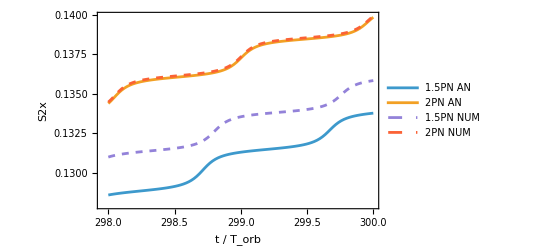

```mathematica
(*TEST S2 SOLUTION : OK*)
data=data1;NumVec=4;NumComp=1;
tmin=298 Torb[data];tmax=tmin+  2 Torb[data];plotIndices={1,2,4,5(*,6*)};Npoints=100;

DefPlot[data,NumVec,NumComp,tmin,tmax,plotIndices,Npoints]
```

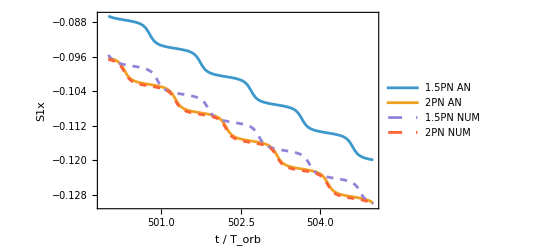

```mathematica
(*TEST S1 SOLUTION : OK*)
data=data1;NumVec=3;NumComp=1;
tmin=500 Torb[data];tmax=tmin+5Torb[data];plotIndices={1,2,4,5(*,6*)};Npoints=100;

DefPlot[data,NumVec,NumComp,tmin,tmax,plotIndices,Npoints]
```

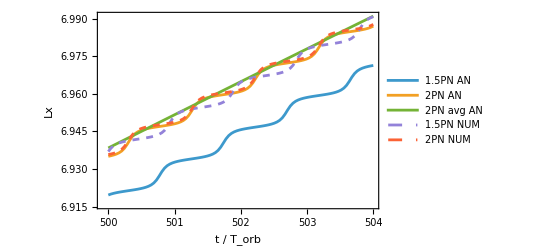

```mathematica
(*TEST L SOLUTION : OK*)
data=data1;NumVec=2;NumComp=1;
tmin=500 Torb[data];tmax=tmin+4Torb[data];plotIndices={1,2,3,4,5(*,6*)};Npoints=100;

DefPlot[data,NumVec,NumComp,tmin,tmax,plotIndices,Npoints]
```

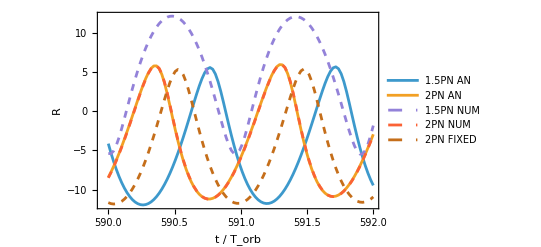

```mathematica
(*TEST Rmag SOLUTION : OK*)
data=data1;NumVec=1;NumComp=3;
tmin=  590  Torb[data];tmax=tmin+2Torb[data];plotIndices={1,2,4,5,6};Npoints=100;

DefPlotNorm[data,NumVec,NumComp,tmin,tmax,plotIndices,Npoints]
```

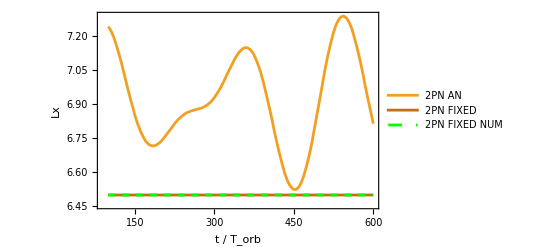

```mathematica
data=data1;NumVec=2;NumComp=1;
tmin=100Torb[data];tmax=tmin+500Torb[data];plotIndices={2,6,7};Npoints=100;

DefPlot[data,NumVec,NumComp,tmin,tmax,plotIndices,Npoints]
```

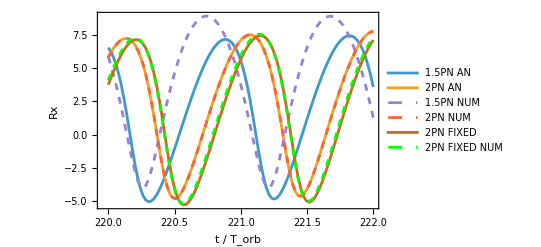

```mathematica
data=data1;NumVec=1;NumComp=1;
tmin=220Torb[data];tmax=tmin+2Torb[data];plotIndices={1,2,4,5,6,7};Npoints=100;

DefPlot[data,NumVec,NumComp,tmin,tmax,plotIndices,Npoints]
```

```mathematica
Speak["Job done"]
```